# 3L Planar PA & Non-Planar NPA family in massive ϕ^3-theory

```mathematica
Quit[]
```

```mathematica
Needs["ThetaDerivatives`"]
```

With this package you can use operators in θ-form.

Use PF to let an operator in θ-form act on a function.

Use ThetaPF to get an operator in θ-form.

Created by Christoph Nega

m::shdw: Symbol m appears in multiple contexts {ThetaDerivatives`,SOFIA`}; definitions in context ThetaDerivatives` may shadow or be shadowed by other definitions.

k::shdw: Symbol k appears in multiple contexts {ThetaDerivatives`,Global`}; definitions in context ThetaDerivatives` may shadow or be shadowed by other definitions.

PF::shdw: Symbol PF appears in multiple contexts {ThetaDerivatives`,Global`}; definitions in context ThetaDerivatives` may shadow or be shadowed by other definitions.

θ::shdw: Symbol θ appears in multiple contexts {ThetaDerivatives`,Global`}; definitions in context ThetaDerivatives` may shadow or be shadowed by other definitions.

```mathematica
Clear[Rotation,Ableitungsbasis]
Rotation[xx_]:=Module[{hi,hii,hiinv},
hi=#[[1]];
hii=#[[2]];
hiinv=Inverse[hii]//Simplify;
hii.(hi.hiinv-D[hiinv,xx])//Simplify]&;
Ableitungsbasis[xx_,ll_]:=Module[{hi,hii,lhi},
hi=#;
lhi=Length[hi];
Do[hi=Rotation[xx][{hi,Table[If[i==kk,hi[[i-1]],Table[If[j==i,1,0],{j,lhi}]],{i,lhi}]}]//Simplify,{kk,2,ll}];
hi]&;
```

```mathematica
Get["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/drawDiagram.m"];
```

## Replacement Roots to Dummy-Functions (z, MUM point variable)

Parameterbereich:         0 < s < 4

Wurzeln ersetzen durch Dummy-Funktionen:

```mathematica
WurzelArgumente={z,1-z,1-4z,1-9z,1-16z};
ListeRational={R1[z],R2[z],R3[z],R4[z],R5[z]};
ListeWurzeln=Table[√WurzelArgumente[[k]],{k,Length[WurzelArgumente]}];
WurzelzuRational=Table[ListeWurzeln[[k]]^i->ListeRational[[k]]^i,{i,{-1,1}},{k,Length[WurzelArgumente]}]//Flatten;
RationalzuWurzel=Table[ListeRational[[k]]->ListeWurzeln[[k]],{k,Length[WurzelArgumente]}];
AlleWurzelnzuRational=Table[RationalzuWurzel[[k,1]]^m__->RationalzuWurzel[[k,2]]^m,{k,Length[WurzelArgumente]}]//Flatten//DeleteDuplicates;
```

Gerade Potenzen der Dummy-Funktionen sind wieder Rational:

```mathematica
Clear[WurzelnSimplify,flipRSigns,DenominatorSimplify]
WurzelnSimplify:=Module[{hi,SimWurzeln},
hi=#;
SimWurzeln=Table[ListeRational[[k]]^m__->WurzelArgumente[[k]]^Floor[m/2] ListeRational[[k]]^(m-2 Floor[m/2]),{k,Length[WurzelArgumente]}]//Flatten//DeleteDuplicates;
hi=ReplaceRepeated[hi,SimWurzeln];
hi]&;
flipRSigns[$X_]:=$X/. {c_?NumericQ:>c,(*leave numbers*)t_/;StringMatchQ[SymbolName[Head[t]],"R*"]:>-t,Times[a___,t_,b___]/;StringMatchQ[SymbolName[Head[t]],"R*"]:>-Times[a,t,b]};
DenominatorSimplify[$X_]:=Module[{hi,hii},
hi=$X//Together//Factor;
hi/.{1/X_:>1/Den[X]}/.{1/X_^2->1/Den[X^2]}/.{1/Den[X_]:>Factor[flipRSigns[X]/WurzelnSimplify[Expand[X flipRSigns[X]]]]}//ExpandNumerator//WurzelnSimplify];
```

Ableitungsregeln der Dummy Funktionen:

```mathematica
D[ListeWurzeln,z]/.AlleWurzelnzuRational//WurzelnSimplify;
Abls=Table[D[ListeRational[[k]],z]->%[[k]],{k,Length[%]}]//DeleteCases[#,0->0]&;
ListeAbleitungenWurzeln=%/.WurzelzuRational//WurzelnSimplify//Simplify
```

{R1'[z]→R1[z]/(2 z),R2'[z]→R2[z]/(2 (-1+z)),R3'[z]→(2 R3[z])/(-1+4 z),R4'[z]→(9 R4[z])/(-2+18 z),R5'[z]→(8 R5[z])/(-1+16 z)}

## Two interesting Sectors: Triangle with two Bubbles & Triangle with a Sunset

In this section we want to analyze just these two integrals with the necessary subsectors.

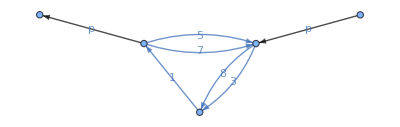

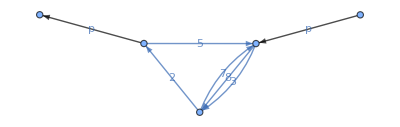

```mathematica
j[PA,{1,0,1,0,1,0,1,1,0}]//drawDiagram(*Triangle with two Bubbles*)
j[PA,{0,1,1,0,1,0,1,1,0}]//drawDiagram(*Triangle with a Sunset*)
```

Getting the input from REDUZE.

```mathematica
InputReduzePANPA=Import["/Users/Chris2106Nega/ReduzeKira/Reduze/MyPrograms/SelfEnergiesOtherTheories/Phi3/3L/deq/deq.m"]/.{d->2-2ϵ,eps->ϵ};(*We do it here directly in two dimensions since all integrals are naturally considered in two dimensions.*)
```

```mathematica
MastersPANPA=Module[{hi},
hi=Table[InputReduzePANPA⟦k⟧,{k,1,Length[InputReduzePANPA],3}];
Table[hi[[k,1,1]],{k,Length[hi]}]];
LMastersPANPA=Length[MastersPANPA];
Print["These are the ", LMastersPANPA," master integrals:"]
MastersPANPA//TableForm
```

These are the 10 master integrals:

INT[PA,3,7,3,0,{1,1,1,0,0,0,0,0,0}]
INT[PA,4,198,4,0,{0,1,1,0,0,0,1,1,0}]
INT[PA,4,71,4,0,{1,1,1,0,0,0,1,0,0}]
INT[PA,4,212,4,0,{0,0,1,0,1,0,1,1,0}]
INT[PA,4,212,5,0,{0,0,2,0,1,0,1,1,0}]
INT[PA,4,212,6,0,{0,0,3,0,1,0,1,1,0}]
INT[PABaikov213,5,31,5,0,{1,1,1,1,1,0,0,0,0}]
INT[PABaikov213,5,31,6,0,{1,1,2,1,1,0,0,0,0}]
INT[PABaikov213,5,31,5,1,{1,1,1,1,1,-1,0,0,0}]
INT[PA,5,214,5,0,{0,1,1,0,1,0,1,1,0}]

Plot of corner integrals for different sectors (original ones):

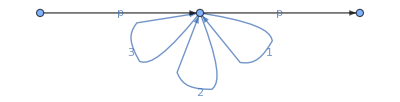
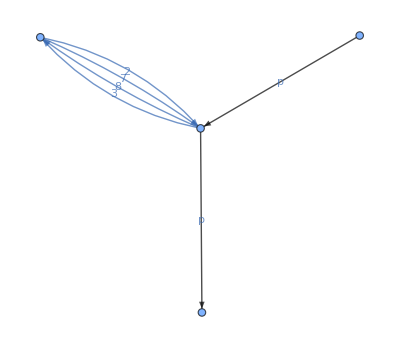
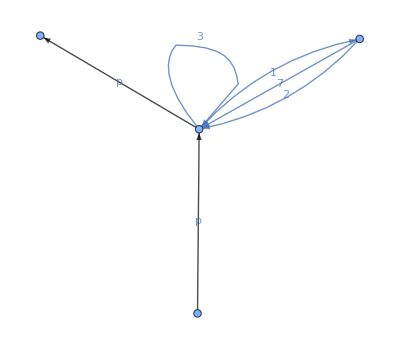
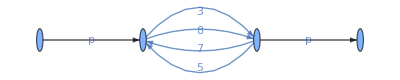
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[j[MastersPANPA[[k,1]]//ToExpression,MastersPANPA[[k,6]]]/.{j[PABaikov213,X_]:>j[PA,{1,0,1,0,1,0,1,1,0}]}//drawDiagram,{k,LMastersPANPA}]//DeleteDuplicates
```

We do not have to include the following graph since it does not couple to the triangle with two bubbles in the differential equation although one could get it via pinching.

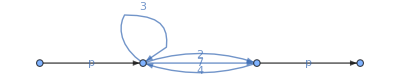

```mathematica
j[PA,{0,1,1,1,0,0,1,0,0}]//drawDiagram
```

GMs:

```mathematica
Table[der[MastersPANPA[[i]],s],{i,LMastersPANPA}]/.InputReduzePANPA;
GMs=Table[Coefficient[%[[i]],MastersPANPA[[j]]],{i,LMastersPANPA},{j,LMastersPANPA}]//Factor;
%//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(1+3 ϵ)/s | -(4 m2)/s | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ((1+3 ϵ) (1+4 ϵ))/(4 m2 s) | (4 m2-s+16 m2 ϵ-s ϵ)/(4 m2 s) | -1/2 | 0 | 0 | 0 | 0
(12 ϵ^3)/(m2 (4 m2-s) (16 m2-s) s) | 0 | 0 | -((1+3 ϵ) (1+4 ϵ) (120 m2^2-28 m2 s+s^2+176 m2^2 ϵ-36 m2 s ϵ+s^2 ϵ))/(8 m2^2 (4 m2-s) (16 m2-s) s) | -(800 m2^3-392 m2^2 s+40 m2 s^2-s^3+3232 m2^3 ϵ-1288 m2^2 s ϵ+104 m2 s^2 ϵ-2 s^3 ϵ+3008 m2^3 ϵ^2-992 m2^2 s ϵ^2+64 m2 s^2 ϵ^2-s^3 ϵ^2)/(8 m2^2 (4 m2-s) (16 m2-s) s) | -(256 m2^3-264 m2^2 s+36 m2 s^2-s^3+256 m2^3 ϵ-384 m2^2 s ϵ+48 m2 s^2 ϵ-s^3 ϵ)/(4 m2 (4 m2-s) (16 m2-s) s) | 0 | 0 | 0 | 0
0 | 0 | -(4 ϵ)/(s (-m2+s)) | (2 (1+3 ϵ))/(s (-m2+s)) | -(2 (-6 m2+s))/(s (-m2+s)) | 0 | -(-2 m2+2 s+5 m2 ϵ+3 s ϵ)/(s (-m2+s)) | -(3 m2)/s | (6 ϵ)/(s (-m2+s)) | 0
(ϵ (-m2-s+3 m2 ϵ+s ϵ))/(m2^2 (m2-s) (9 m2-s) s) | 0 | -(2 ϵ (36 m2-2 s+9 m2 ϵ+5 s ϵ))/(3 m2 (m2-s) (9 m2-s) s) | -((1+3 ϵ) (-54 m2^2-10 m2 s+s^2+36 m2^2 ϵ-60 m2 s ϵ+4 s^2 ϵ))/(6 m2^2 (m2-s) (9 m2-s) s) | (360 m2^3+64 m2^2 s-24 m2 s^2+s^3+304 m2^2 s ϵ-44 m2 s^2 ϵ+s^3 ϵ)/(6 m2^2 (m2-s) (9 m2-s) s) | ((4 m2-s) (16 m2-s))/(3 m2 (m2-s) (9 m2-s)) | -(-36 m2^2+23 m2 s-s^2+54 m2^2 ϵ+45 m2 s ϵ-s^2 ϵ+36 m2^2 ϵ^2+22 m2 s ϵ^2+2 s^2 ϵ^2)/(3 m2 (m2-s) (9 m2-s) s) | -(2 (-9 m2^2+5 m2 s-9 m2^2 ϵ+s^2 ϵ))/(s (-9 m2+s) (-m2+s)) | (2 ϵ (18 m2-s+9 m2 ϵ+s ϵ))/(m2 (m2-s) (9 m2-s) s) | 0
0 | 0 | -((3 m2+s) ϵ)/(s (-m2+s)) | -(2 m2 (1+3 ϵ))/((m2-s) s) | -(2 (-18 m2^2+2 m2 s+s^2))/(3 s (-m2+s)) | 0 | -(-6 m2^2+5 m2 s+s^2+12 m2^2 ϵ+10 m2 s ϵ+2 s^2 ϵ)/(3 s (-m2+s)) | -(m2 (3 m2+s))/s | ((5 m2+s) ϵ)/(s (-m2+s)) | 0
0 | ϵ/(s (-4 m2+s)) | 0 | -(1+4 ϵ)/(s (-4 m2+s)) | (6 m2)/((4 m2-s) s) | 0 | 0 | 0 | 0 | -(-2 m2+s+s ϵ)/(s (-4 m2+s)))

GMm12:

```mathematica
Table[der[MastersPANPA[[i]],m2],{i,LMastersPANPA}]/.InputReduzePANPA;
GMm2=Table[Coefficient[%[[i]],MastersPANPA[[j]]],{i,LMastersPANPA},{j,LMastersPANPA}]//Factor;
%//MatrixForm
```

(-(3 ϵ)/m2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(1+3 ϵ)/m2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(1+3 ϵ)/m2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -((1+3 ϵ) (1+4 ϵ))/(4 m2^2) | -(12 m2-s+28 m2 ϵ-s ϵ)/(4 m2^2) | s/(2 m2) | 0 | 0 | 0 | 0
-(12 ϵ^3)/(m2^2 (4 m2-s) (16 m2-s)) | 0 | 0 | ((1+3 ϵ) (1+4 ϵ) (120 m2^2-28 m2 s+s^2+176 m2^2 ϵ-36 m2 s ϵ+s^2 ϵ))/(8 m2^3 (4 m2-s) (16 m2-s)) | (800 m2^3-392 m2^2 s+40 m2 s^2-s^3+3232 m2^3 ϵ-1288 m2^2 s ϵ+104 m2 s^2 ϵ-2 s^3 ϵ+3008 m2^3 ϵ^2-992 m2^2 s ϵ^2+64 m2 s^2 ϵ^2-s^3 ϵ^2)/(8 m2^3 (4 m2-s) (16 m2-s)) | -(512 m2^3+24 m2^2 s-24 m2 s^2+s^3+512 m2^3 ϵ+144 m2^2 s ϵ-36 m2 s^2 ϵ+s^3 ϵ)/(4 m2^2 (4 m2-s) (16 m2-s)) | 0 | 0 | 0 | 0
0 | 0 | -(4 ϵ)/(m2 (m2-s)) | (2 (1+3 ϵ))/(m2 (m2-s)) | (2 (6 m2-s))/(m2 (m2-s)) | 0 | -(8 ϵ)/(m2-s) | 3 | (6 ϵ)/(m2 (m2-s)) | 0
-(ϵ (-m2-s+3 m2 ϵ+s ϵ))/(m2^3 (m2-s) (9 m2-s)) | 0 | (2 ϵ (36 m2-2 s+9 m2 ϵ+5 s ϵ))/(3 m2^2 (m2-s) (9 m2-s)) | ((1+3 ϵ) (-54 m2^2-10 m2 s+s^2+36 m2^2 ϵ-60 m2 s ϵ+4 s^2 ϵ))/(6 m2^3 (m2-s) (9 m2-s)) | -(360 m2^3+64 m2^2 s-24 m2 s^2+s^3+304 m2^2 s ϵ-44 m2 s^2 ϵ+s^3 ϵ)/(6 m2^3 (m2-s) (9 m2-s)) | -((4 m2-s) (16 m2-s) s)/(3 m2^2 (m2-s) (9 m2-s)) | (-36 m2^2+23 m2 s-s^2+54 m2^2 ϵ+45 m2 s ϵ-s^2 ϵ+36 m2^2 ϵ^2+22 m2 s ϵ^2+2 s^2 ϵ^2)/(3 m2^2 (m2-s) (9 m2-s)) | -(45 m2^2-40 m2 s+3 s^2+45 m2^2 ϵ-30 m2 s ϵ+s^2 ϵ)/(m2 (m2-s) (9 m2-s)) | -(2 ϵ (18 m2-s+9 m2 ϵ+s ϵ))/(m2^2 (m2-s) (9 m2-s)) | 0
0 | 0 | -((3 m2+s) ϵ)/(m2 (m2-s)) | (2 (1+3 ϵ))/(m2-s) | (2 (18 m2^2-2 m2 s-s^2))/(3 m2 (m2-s)) | 0 | -(-6 m2^2+5 m2 s+s^2+12 m2^2 ϵ+10 m2 s ϵ+2 s^2 ϵ)/(3 m2 (m2-s)) | 3 m2+s | (-m2+s+2 m2 ϵ+4 s ϵ)/(m2 (m2-s)) | 0
0 | ϵ/(m2 (4 m2-s)) | 0 | -(1+4 ϵ)/(m2 (4 m2-s)) | -6/(4 m2-s) | 0 | 0 | 0 | 0 | -((6 m2-s) (1+2 ϵ))/(m2 (4 m2-s)))

Checks:

```mathematica
D[GMs,m2]-D[GMm2,s]-(GMm2.GMs-GMs.GMm2)//Simplify//Flatten//Union
s GMs+m2 GMm2-DiagonalMatrix[1/2 Table[InputReduzePANPA[[k,2]]/._INT->1//Factor,{k,3,Length[InputReduzePANPA],3}]]//Simplify//Simplify//Flatten//Union
```

{0}

{0}

Everything is fine!

Sizes of the different sectors:

```mathematica
MITally=MastersPANPA/.{INT[X_,Y_,Z_,U__]->INT[X,Y,Z]}//Tally//SortBy[#,#[[2]]&]&//Reverse;
Table[{"Number of master integrals in a sector",k,"Number of sectors of that type",Length[Cases[MITally,{_INT,k}]]},{k,5}]//TableForm
```

Number of master integrals in a sector | 1 | Number of sectors of that type | 4
Number of master integrals in a sector | 2 | Number of sectors of that type | 0
Number of master integrals in a sector | 3 | Number of sectors of that type | 2
Number of master integrals in a sector | 4 | Number of sectors of that type | 0
Number of master integrals in a sector | 5 | Number of sectors of that type | 0

Start differential equation at the MUM point.

We take for simplicity from now on m2=1. Moreover, we go to the MUM point of the Calabi-Yau geometries which is a z=1/s.

```mathematica
GMzPANPA=-(1/z)^2 GMs/.{m2->1,s->1/z}//Collect[#,ϵ,Factor]&;
%//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/z+(3 ϵ)/z | 4/z | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/(4 z)-(7 ϵ)/(4 z)-(3 ϵ^2)/z | -(-1+4 z)/(4 z^2)-((-1+16 z) ϵ)/(4 z^2) | 1/(2 z^2) | 0 | 0 | 0 | 0
-(12 z ϵ^3)/((-1+4 z) (-1+16 z)) | 0 | 0 | (1-28 z+120 z^2)/(8 z (-1+4 z) (-1+16 z))+((1-29 z+127 z^2) ϵ)/(z (-1+4 z) (-1+16 z))+((19-588 z+2672 z^2) ϵ^2)/(8 z (-1+4 z) (-1+16 z))+(3 (1-36 z+176 z^2) ϵ^3)/(2 z (-1+4 z) (-1+16 z)) | (-1+40 z-392 z^2+800 z^3)/(8 z^2 (-1+4 z) (-1+16 z))+((-1+52 z-644 z^2+1616 z^3) ϵ)/(4 z^2 (-1+4 z) (-1+16 z))+((1-60 z+752 z^2) ϵ^2)/(8 z^2 (-1+16 z)) | (-1+36 z-264 z^2+256 z^3)/(4 z^2 (-1+4 z) (-1+16 z))+((-1+48 z-384 z^2+256 z^3) ϵ)/(4 z^2 (-1+4 z) (-1+16 z)) | 0 | 0 | 0 | 0
0 | 0 | -(4 ϵ)/(-1+z) | 2/(-1+z)+(6 ϵ)/(-1+z) | (2 (-1+6 z))/((-1+z) z) | 0 | 2/z-((3+5 z) ϵ)/((-1+z) z) | 3/z | (6 ϵ)/(-1+z) | 0
((1+z) ϵ)/((-1+z) (-1+9 z))-((1+3 z) ϵ^2)/((-1+z) (-1+9 z)) | 0 | (4 (-1+18 z) ϵ)/(3 (-1+z) (-1+9 z))+(2 (5+9 z) ϵ^2)/(3 (-1+z) (-1+9 z)) | -(-1+10 z+54 z^2)/(6 (-1+z) z (-1+9 z))-((-7+90 z+126 z^2) ϵ)/(6 (-1+z) z (-1+9 z))+(2 (1-15 z+9 z^2) ϵ^2)/((-1+z) z (-1+9 z)) | -(1-24 z+64 z^2+360 z^3)/(6 (-1+z) z^2 (-1+9 z))-((1-44 z+304 z^2) ϵ)/(6 (-1+z) z^2 (-1+9 z)) | -((-1+4 z) (-1+16 z))/(3 (-1+z) z^2 (-1+9 z)) | -(1-23 z+36 z^2)/(3 (-1+z) z (-1+9 z))+((-1+45 z+54 z^2) ϵ)/(3 (-1+z) z (-1+9 z))+(2 (1+2 z) (1+9 z) ϵ^2)/(3 (-1+z) z (-1+9 z)) | -(2 (-5+9 z))/((-1+z) (-1+9 z))-(2 (-1+3 z) (1+3 z) ϵ)/((-1+z) z (-1+9 z)) | -(2 (-1+18 z) ϵ)/((-1+z) (-1+9 z))-(2 (1+9 z) ϵ^2)/((-1+z) (-1+9 z)) | 0
0 | 0 | -((1+3 z) ϵ)/((-1+z) z) | 2/(-1+z)+(6 ϵ)/(-1+z) | (2 (-1-2 z+18 z^2))/(3 (-1+z) z^2) | 0 | (1+6 z)/(3 z^2)-(2 (1+2 z) (1+3 z) ϵ)/(3 (-1+z) z^2) | (1+3 z)/z^2 | ((1+5 z) ϵ)/((-1+z) z) | 0
0 | ϵ/(-1+4 z) | 0 | -1/(-1+4 z)-(4 ϵ)/(-1+4 z) | -6/(-1+4 z) | 0 | 0 | 0 | 0 | (-1+2 z)/(z (-1+4 z))-ϵ/(z (-1+4 z)))

ϵ-factorization purely from the differential equation.

We start with the relations that we need for the new transcendental functions.

```mathematica
RelPFSunset=PF[z][ω02LSun[z],1-3 z+2 (-1+5 z) θ+(-1+z) (-1+9 z) θ^2]//Solve[#==0,ω02LSun''[z]]&//Collect[#,{ω02LSun[z],ω02LSun'[z]},Factor]&//Flatten;
RelPFBanana=PF[z][ω03LBan[z],-1+4 z-3 (-1+6 z) θ+3 (-1+10 z) θ^2+(-1+4 z) (-1+16 z) θ^3]//Solve[#==0,ω03LBan'''[z]]&//Collect[#,{ω03LBan[z],ω03LBan'[z],ω03LBan''[z],ϵ},Factor]&//Flatten;
RelGriffiths={ω03LBan''[z]->((-1+8 z) ω03LBan[z])/(2 z^2 (-1+4 z) (-1+16 z))-(2 (-5+32 z) ω03LBan'[z])/((-1+4 z) (-1+16 z))+ω03LBan'[z]^2/(2 ω03LBan[z])};
RelNew={GG1'[z]->-(2 (-1+8 z) (1+8 z)^3)/(z^2 (-1+4 z)^2 (-1+16 z)^2)ω03LBan[z]^2,GG2'[z]->(R3[z]R5[z]GG1[z])/((1-4z)(1-16z) ω03LBan[z]),(*additional new functions of third kind type*)GG3'[z]->ω03LBan[z] (-((3-5 z+12 z^2) ω02LSun[z])/(2 (-1+z) z^2 (-1+9 z))+((2-5 z+23 z^2) ω02LSun'[z])/((-1+z) z (-1+9 z))),GG4'[z]->(z GG3[z])/((-1+z) (-1+9 z) ω02LSun[z]^2)-((2-5 z+23 z^2) ω03LBan[z])/((-1+z)^2 (-1+9 z)^2 ω02LSun[z]),GG5'[z]->(GG3[z] R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z]),GG6'[z]->-((1-10 z+53 z^2+100 z^3+576 z^4) GG3[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))-(GG1[z] GG5[z] R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z])+ω03LBan[z] (((5-90 z+162 z^2-90 z^3+333 z^4) ω02LSun[z])/(2 (-1+z)^2 z^2 (-1+9 z)^2)-(2 (2-5 z+23 z^2) ω02LSun'[z])/((-1+z) z (-1+9 z))),GG7'[z]->((1+4 z) ω03LBan[z])/((-1+z)^2 z),GG8'[z]->((1+z) ω02LSun[z])/z^2,GG9'[z]->((1+2 z) R3[z] ω03LBan[z])/(z (-1+4 z)^2)};
```

Canonicalization:

```mathematica
RotCan1=IdentityMatrix[LMastersPANPA];
RotCan2=IdentityMatrix[LMastersPANPA];
RotCan3=IdentityMatrix[LMastersPANPA];
(**)
(*Rotation 1: Derivative basis and a small clean up.*)
RotCan1[[4;;9,4;;9]]=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {(5 z (-1+2 z))/(2 (-1+z) (-1+9 z)), 0, 0, 1, 0, 0}, {-1/(2 (-1+z) (-1+9 z))-(2-5 z+23 z^2)/((-1+z)^2 (-1+9 z)^2)0+ϵ(-(2 (2-5 z+23 z^2))/((-1+z)^2 (-1+9 z)^2)), (5 z (-1+2 z))/(2 (-1+z) (-1+9 z)), 0, 0, 1, 0}, {5/(6 (-1+z)), 0, 0, -(1+3 z)/(3 z), 0, 1}}).({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {-1/(4 z^3)-ϵ/z^3-(3 ϵ^2)/(4 z^3), -(-1+4 z)/(4 z^2)-((-1+4 z) ϵ)/(4 z^2), 2/z^3, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0}, {1/z+(3 ϵ)/z, 4/z, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {2/(-1+z)+(6 ϵ)/(-1+z), (2 (-1+6 z))/((-1+z) z), 0, 2/z-((3+5 z) ϵ)/((-1+z) z), 3/z, (6 ϵ)/(-1+z)}, {0, 0, 0, 0, 0, 1}});(*Derivative basis for the 3L Banana sector and Triangle Bubble. Moreover, some clean up to make explizit the third kind functions.*)
RotCan1[[8,3]]=-(4 ϵ)/(-1+z)(*For full derivative also on this subsector.*);
RotCan1[[10,4]]=(3 z)/(2 (-1+4 z))(*To simplify a bit the last integral on a subsetor.*);
(**)
(*Rotation 2: ϵ-form on the diagonal blocks/max cuts.*)
RotCan2[[4;;6,4;;6]]=1/ϵ^2({{1, 0, 0}, {(2 (-1+10 z) R3[z] R5[z] ω03LBan[z])/(z (-1+4 z) (-1+16 z)), 1, 0}, {-((-7+168 z-800 z^2+512 z^3+4096 z^4) ω03LBan[z]^2)/(2 z^2 (-1+4 z) (-1+16 z))+(-(2 (-1+30 z-228 z^2+640 z^3) ω03LBan[z]^2)/(z^2 (-1+4 z) (-1+16 z))+(2 (-1+10 z) ω03LBan[z] ω03LBan'[z])/z)/ϵ, (4 (-1+10 z) R3[z] R5[z] ω03LBan[z])/(z (-1+4 z) (-1+16 z)), 1}}).({{ϵ^2, 0, 0}, {0, ϵ, 0}, {0, 0, 1}}).Inverse[({{ω03LBan[z], 0, 0}, {ω03LBan'[z], (R3[z]R5[z])/((1-4z)(1-16z)), 0}, {ω03LBan''[z], (R3[z]R5[z])/((1-4z)(1-16z))ω03LBan'[z]/ω03LBan[z]+D[(R3[z]R5[z])/((1-4z)(1-16z)),z], 1/(ω03LBan[z](1-4z)(1-16z))}})]/.ListeAbleitungenWurzeln/.RelGriffiths;(*Rotations for 3L Banana max cut sector up to new G-functions. Final ϵ-rescaling to adjust for the relative scaling in ϵ between the different sectors.*)
RotCan2[[7;;9,7;;9]]=1/ϵ({{1, 0, 0}, {-(-1/2(-3+10 z+9 z^2)/z^2 ω02LSun[z]^2), 1, 0}, {0, 0, 1}}).({{ϵ, 0, 0}, {0, 1, 0}, {0, 0, ϵ}}).Inverse[({{ω02LSun[z], 0, 0}, {ω02LSun'[z], z/((1-z) (1-9 z)ω02LSun[z]), 0}, {0, 0, 1}})];(*Rotations for 2L Sunset max cut sector. Final ϵ-rescaling to adjust for the relative scaling in ϵ between the different sectors.*)
RotCan2[[10,10]]=R3[z]/z;(*Rotation for the last integral.*)
(**)
(*Rotation 3: full ϵ-form with introduction of new G-functions.*)
RotCan3[[4;;9,4;;9]]=({{1, 0, 0, 0, 0, 0}, {GG2[z], 1, 0, 0, 0, 0}, {-1/2 GG2[z]^2, -GG2[z], 1, 0, 0, 0}, {-GG4[z], 0, 0, 1, 0, 0}, {-GG6[z], GG5[z], 0, 0, 1, 0}, {1/6 GG7[z], 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {GG1[z]/ϵ, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {-GG3[z]/ϵ, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {1/ϵ(-(2-5 z+23 z^2)/((-1+z) z (-1+9 z)))ω03LBan[z] ω02LSun[z]0-(2 (2-5 z+23 z^2))/((-1+z) z (-1+9 z))ω02LSun[z] ω03LBan[z]0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}});(*G-functions for the 3L Banana and the Triangle with two Bubbles and the mixings between these sectors.*)
RotCan3[[8,1]]=-3GG8[z];(*Second master of Triangle Bubbles to the Tadpole.*)
RotCan3[[10,4]]=1/2 GG9[z];(*Triangle Sunset to the 3L Banana.*)
```

```mathematica
RotCan=RotCan3.RotCan2.RotCan1;
RotCanInverse=Inverse[%]//Factor;
```

```mathematica
GMzEps=RotCan.(GMzPANPA.RotCanInverse-D[RotCanInverse,z])/.ListeAbleitungenWurzeln/.RelPFSunset/.RelPFBanana/.RelGriffiths/.RelNew/.{HH1'[z]->((2-5 z+23 z^2) ω03LBan[z])/((-1+z)^2 (-1+9 z)^2),HH2'[z]->((-1+3 z) HH1[z] ω02LSun[z])/z^3+((3-5 z+12 z^2) ω02LSun[z] ω03LBan[z])/(2 (-1+z) z^2 (-1+9 z))}//Factor//WurzelnSimplify//Collect[#,{ϵ,ω02LSun[z],ω02LSun'[z],ω03LBan[z],ω03LBan'[z],GG1[z],GG2[z]},Factor]&//WurzelnSimplify//Collect[#,{ϵ,ω02LSun[z],ω02LSun'[z],ω03LBan[z],ω03LBan'[z],GG1[z],GG2[z]},Factor]&;
FreeQ[%/ϵ//Expand,ϵ,∞]
GMzEps//MatrixForm
```

True

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ϵ (-(2 (-1+10 z))/(z (-1+4 z) (-1+16 z))-(GG2[z] R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z])) | (ϵ R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z]) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ϵ (-(3 GG2[z]^2 R3[z] R5[z])/(2 (-1+4 z) (-1+16 z) ω03LBan[z])+((1+8 z)^2 (1-8 z+64 z^2) R3[z] R5[z] ω03LBan[z])/(2 z^2 (-1+4 z)^2 (-1+16 z)^2)) | ϵ (-(2 (-1+10 z))/(z (-1+4 z) (-1+16 z))+(2 GG2[z] R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z])) | (ϵ R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z]) | 0 | 0 | 0 | 0
-(24 ϵ ω03LBan[z])/z^2 | 0 | 0 | ϵ ((GG2[z]^3 R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z])-((1+8 z)^2 (1-8 z+64 z^2) GG2[z] R3[z] R5[z] ω03LBan[z])/(z^2 (-1+4 z)^2 (-1+16 z)^2)-(8 (-1+8 z) (1+8 z)^3 ω03LBan[z]^2)/(z^2 (-1+4 z)^2 (-1+16 z)^2)) | ϵ (-(3 GG2[z]^2 R3[z] R5[z])/(2 (-1+4 z) (-1+16 z) ω03LBan[z])+((1+8 z)^2 (1-8 z+64 z^2) R3[z] R5[z] ω03LBan[z])/(2 z^2 (-1+4 z)^2 (-1+16 z)^2)) | ϵ (-(2 (-1+10 z))/(z (-1+4 z) (-1+16 z))-(GG2[z] R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z])) | 0 | 0 | 0 | 0
(3 z ϵ GG8[z])/((-1+z) (-1+9 z) ω02LSun[z]^2) | 0 | 0 | ϵ (-((1-10 z+53 z^2+100 z^3+576 z^4) GG4[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))+((z GG2[z] GG5[z])/((-1+z) (-1+9 z))+(z GG6[z])/((-1+z) (-1+9 z)))/ω02LSun[z]^2+(GG2[z] GG4[z] R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z])+(2 (2-5 z+23 z^2) ω03LBan[z])/((-1+z)^2 (-1+9 z)^2 ω02LSun[z])) | ϵ (-(z GG5[z])/((-1+z) (-1+9 z) ω02LSun[z]^2)-(GG4[z] R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z])) | 0 | -((-3+10 z+9 z^2) ϵ)/(2 (-1+z) z (-1+9 z)) | (z ϵ)/((-1+z) (-1+9 z) ω02LSun[z]^2) | 0 | 0
ϵ (-(3 (-3+10 z+9 z^2) GG8[z])/(2 (-1+z) z (-1+9 z))-(3 (1+3 z) ω02LSun[z])/z^2) | 0 | (4 ϵ ω02LSun[z])/z^2 | ϵ (-((1-10 z+53 z^2+100 z^3+576 z^4) GG2[z] GG5[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))-((1-10 z+53 z^2+100 z^3+576 z^4) GG6[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))+((1+3 z)^4 GG4[z] ω02LSun[z]^2)/(4 (-1+z) z^3 (-1+9 z))+(-(GG2[z]^2 GG5[z] R3[z] R5[z])/(2 (-1+4 z) (-1+16 z))+(GG2[z] GG6[z] R3[z] R5[z])/((-1+4 z) (-1+16 z)))/ω03LBan[z]+((1+8 z)^2 (1-8 z+64 z^2) GG5[z] R3[z] R5[z] ω03LBan[z])/(2 z^2 (-1+4 z)^2 (-1+16 z)^2)-((-1-20 z-16 z^2+240 z^3+117 z^4) ω02LSun[z] ω03LBan[z])/((-1+z)^2 z^2 (-1+9 z)^2)) | ϵ (((1-10 z+53 z^2+100 z^3+576 z^4) GG5[z])/(2 (-1+z) z (-1+4 z) (-1+9 z) (-1+16 z))+((GG2[z] GG5[z] R3[z] R5[z])/((-1+4 z) (-1+16 z))-(GG6[z] R3[z] R5[z])/((-1+4 z) (-1+16 z)))/ω03LBan[z]) | (ϵ GG5[z] R3[z] R5[z])/((-1+4 z) (-1+16 z) ω03LBan[z]) | ((1+3 z)^4 ϵ ω02LSun[z]^2)/(4 (-1+z) z^3 (-1+9 z)) | -((-3+10 z+9 z^2) ϵ)/(2 (-1+z) z (-1+9 z)) | 0 | 0
0 | 0 | ((1+3 z) ϵ)/(3 (-1+z) z) | ϵ (((-1+3 z+24 z^2+64 z^3) GG7[z])/(6 (-1+z) z (-1+4 z) (-1+16 z))-(GG2[z] GG7[z] R3[z] R5[z])/(6 (-1+4 z) (-1+16 z) ω03LBan[z])+((1+4 z) ω03LBan[z])/(3 (-1+z)^2 z)) | (ϵ GG7[z] R3[z] R5[z])/(6 (-1+4 z) (-1+16 z) ω03LBan[z]) | 0 | 0 | 0 | -((1+z) ϵ)/((-1+z) z) | 0
0 | (ϵ R3[z])/(z (-1+4 z)) | 0 | ϵ (-GG9[z]/(2 z (-1+16 z))-(GG2[z] GG9[z] R3[z] R5[z])/(2 (-1+4 z) (-1+16 z) ω03LBan[z])+((1+2 z) R3[z] ω03LBan[z])/(z (-1+4 z)^2)) | (ϵ GG9[z] R3[z] R5[z])/(2 (-1+4 z) (-1+16 z) ω03LBan[z]) | 0 | 0 | 0 | 0 | -ϵ/(z (-1+4 z)))

Start basis after derivative basis and some clean up.

```mathematica
({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {-(24 ϵ^3)/(z^2 (-1+4 z) (-1+16 z)), 0, 0, -1/(z^3 (-1+16 z))-(6 (-1+3 z) ϵ)/(z^3 (-1+4 z) (-1+16 z))-((-11+14 z) ϵ^2)/(z^3 (-1+4 z) (-1+16 z))+(6 (1+2 z) ϵ^3)/(z^3 (-1+4 z) (-1+16 z)), -(1-8 z+64 z^2)/(z^2 (-1+4 z) (-1+16 z))-(6 ϵ)/(z^2 (-1+4 z) (-1+16 z))+((11+16 z) ϵ^2)/(z^2 (-1+16 z)), -(6 (-5+32 z))/((-1+4 z) (-1+16 z))-(6 (-1+10 z) ϵ)/(z (-1+4 z) (-1+16 z)), 0, 0, 0, 0}, {0, 0, 0, -(2-5 z+23 z^2)/((-1+z)^2 (-1+9 z)^2)+(2 (2-5 z+23 z^2) ϵ)/((-1+z)^2 (-1+9 z)^2), 0, 0, 0, 1, 0, 0}, {(3 (1+z) ϵ)/((-1+z) z (-1+9 z))-(3 (1+3 z) ϵ^2)/((-1+z) z (-1+9 z)), 0, (4 ϵ^2)/((-1+z) z (-1+9 z)), -(3-5 z+12 z^2)/(2 (-1+z)^2 z (-1+9 z)^2)+((-1-55 z+61 z^2+95 z^3+540 z^4) ϵ)/(2 (-1+z)^3 z (-1+9 z)^3)-((-7+15 z-117 z^2+425 z^3+324 z^4) ϵ^2)/((-1+z)^3 z (-1+9 z)^3), 0, 0, (-1+3 z)/((-1+z) z^2 (-1+9 z))+((-3+5 z) ϵ)/((-1+z) z^2 (-1+9 z))-(2 (1+z) ϵ^2)/((-1+z) z^2 (-1+9 z)), -((-1+3 z) (1+3 z))/((-1+z) z (-1+9 z))-((-3+10 z+9 z^2) ϵ)/((-1+z) z (-1+9 z)), 0, 0}, {0, 0, ((1+3 z) ϵ)/(3 (-1+z) z), -(1+4 z)/(6 (-1+z)^2 z)+((1+4 z) ϵ)/(3 (-1+z)^2 z), 0, 0, 0, 0, -((1+z) ϵ)/((-1+z) z), 0}, {0, ϵ/(-1+4 z), 0, -(1+2 z)/(2 (-1+4 z)^2)+((1+2 z) ϵ)/(-1+4 z)^2, 0, 0, 0, 0, 0, (-1+2 z)/(z (-1+4 z))-ϵ/(z (-1+4 z))}});
```

## Integrand analysis

```mathematica
Get["/Users/Chris2106Nega/Desktop/Mathematica/SOFIA.m"]
```

Singularities of Feynman Integrals Automatized (v1.0.0.)

.oooooo..o   .oooooo.   oooooooooooo ooooo       .o.       
d8P'    `Y8  d8P'  `Y8b  `888'     `8 `888'      .888.      
Y88bo.      888      888  888          888      .8"888.     
 `"Y8888o.  888      888  888oooo8     888     .8' `888.    
     `"Y88b 888      888  888    "     888    .88ooo8888.   
oo     .d8P `88b    d88'  888          888   .8'     `888.  
8""88888P'   `Y8bood8P'  o888o        o888o o88o     o8888o|

Copyright © 2025 Miguel Correia, Mathieu Giroux, and Sebastian Mizera. All rights reserved.

Most important documented functions:

FeynmanDraw: Running this function will trigger a drawing window, allowing you to draw your diagram with your mouse. The output is the corresponding list of edges and nodes for the diagram.
FeynmanPlot: Plots the input diagram.
SOFIABaikov: Returns the optimized LBL Baikov representation for an input diagram (list of edges and nodes).
SOFIA: Returns the singularities or letters depending on options.
SOFIADecomposeAlphabet: SOFIADecomposeAlphabet[LetterToDecompose,SymbolData] - decomposes the letter LetterToDecompose in terms of the alphabet provided in SymbolData.
SolvePolynomialSystem: Solves a polynomial system using the method specified by Solver->{FastFubini, momentumPLD} option.
Subtopologies: Generates non-trivial subtopologies.
SymmetryQuotient: Given a list of diagrams, returns a reduced list of diagrams with a symmetry map.

## Triangle with two Bubbles

```mathematica
edges={{{1,3},m},{{1,3},m},{{2,3},m}, {{2,1},m}, {{2,1},m}};
nodes={{1,p},{2,-p}};
```

```mathematica
testsofia=SOFIABaikov[{edges,nodes},LoopEdges->{1,3,5},(*LoopEdges->Automatic ,*)Dimension->2-2ϵ,(*MaxCut->True ,*)ShowXs->True ,ShowDetailedDiagram->True]/.Gamma[x___]->1/.ϵ->0/.Wedge[x___]->1/.{ν[1]->1,ν[2]->1,ν[3]->1,ν[4]->1,ν[5]->1}/.ν[i_]->0//Simplify//PowerExpand(*/.d[x_]->1*)
```

x's in terms of dot products:{x1→-m^2+l_1·l_1,x2→-m^2+l_1·l_1+2 l_1·l_2+l_2·l_2,x3→-m^2+l_2·l_2,x4→-m^2+l_2·l_2+2 l_2·l_3+l_3·l_3,x5→-m^2+s+l_3·l_3-2 l_3·p_1,x6→l_3·l_3}

{-Graphics-,-Graphics-}

"Total runtime= "  0.450055

-ⅈ/(π^(3/2) x1 x2 x3 √(3 m^4-x1^2-(x2-x3)^2+2 x1 (x2+x3)+2 m^2 (x1+x2+x3)) x4 x5 √(-x3^2-x4^2+2 x4 x6+(4 m^2-x6) x6+2 x3 (x4+x6)) √(-m^4-s^2-(x5-x6)^2+2 m^2 (s-x5+x6)+2 s (x5+x6)))

Max Cut analysis:

```mathematica
int=(-I √3 π^(3/2))testsofia x1 x2 x3 x4 x5/.{x1->0,x2->0,x3->0,x4->0,x5->0}/.{s->1/z,m->1}/.{1/√X_:>1/√Factor[X]}//PowerExpand//Factor;
%/.{x6->X1}
```

z/(√(-4+X1) √X1 √(1-2 z-2 X1 z+z^2-2 X1 z^2+X1^2 z^2))

We find an elliptic curve which is esactly the one from the sunset. 
The basis consists of the first kind form, the derivative of it and the third kind form.

Just MPL on max cut.

Full analysis, no cut:

```mathematica
int=( π^(3/2))testsofia/.{s->1/z,m->1}/.{s->1/z,m->1}/.{1/√X_:>1/√Factor[X]}//PowerExpand//Factor
```

-z/(x1 x2 x3 √(3+2 x1-x1^2+2 x2+2 x1 x2-x2^2+2 x3+2 x1 x3+2 x2 x3-x3^2) x4 x5 √(-x3^2+2 x3 x4-x4^2+4 x6+2 x3 x6+2 x4 x6-x6^2) √(1-2 z-2 x5 z-2 x6 z+z^2+2 x5 z^2+x5^2 z^2-2 x6 z^2-2 x5 x6 z^2+x6^2 z^2))

```mathematica
Integrate[int ,x1];
Integrate[%/._ArcTanh->1,x2];
Integrate[%/._ArcTan->1,x4];
Integrate[%/._ArcTan->1,x5]//Factor;
Coefficient[%,Log[x5](*There are multiple logs but they all have the same LS.*)]/.{x3->X1-1,x6->X2}/.{1/√X_:>1/√Factor[X]}//PowerExpand
```

z/(√(-4+X1) (-1+X1) √X1 √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2))

This is exactly the holomorphic differential form of the K3 surfaces appearing in the 3L Banana with an additional single pole at X1=1.

```mathematica
z/(√(-4+X1) √X1 √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2))
```

When we compute the residue around this pole we go back to the max cut and find the elliptic curve of the 2L Sunset.

```mathematica
z/(√(-4+X1) (-1+X1) √X1 √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2))(√3 I)//Series[#,{X1,1,-1},Assumptions->X1>0]&//Residue[#,{X1,1}]/.{1/√X_:>1/√Factor[X]}&//PowerExpand;
%/.X2->X1
```

z/(√(-4+X1) √X1 √(1-2 z-2 X1 z+z^2-2 X1 z^2+X1^2 z^2))

So we see that this integral consists on its subcut of a generalized third kind differential form on the K3 surface. This differential form has of course additional cycles and therefore LSs that we have to remove to obtain a canonical integral. 
To see this explicitly, we compute the “torus period” for this differential form and for this a Picard-Fuchs operator.

Various torus periods:

Elliptic curve:		holomorphic period of the Sunset

```mathematica
$ord=75;
toseries=z/(√(-4+X1) √X1 √(1-2 z-2 X1 z+z^2-2 X1 z^2+X1^2 z^2));
t0=Now;
rootseriess=Series[1/(1+ z)^(1/2),{z,0,$ord}]//Normal//#/.{z->-2 (1+X1) z+(-1+X1)^2 z^2}&//Series[#,{z,0,$ord}]&//PowerExpand//Collect[#,{z},Together]&;
toseries=toseries/.{1/(1-2 z-2 X1 z+z^2-2 X1 z^2+X1^2 z^2)^(1/2)->rootseriess}//PowerExpand//Collect[#,{z},Together]/.z^k_:>0/;k>$ord&;
Print["Done series in z!"];
Series[(-1/Y1^2)%%/.{X1->1/Y1},{Y1,0,-1},Assumptions->{Y1>0}]//Normal//Residue[#,{Y1,0}]&//Collect[#,z]&;
holperiod2LSun=%/(Coefficient[%,z,Exponent[%,z,Min]])//Expand
Now-t0
```

Done series in z!

z+3 z^2+15 z^3+93 z^4+639 z^5+4653 z^6+35169 z^7+272835 z^8+2157759 z^9+17319837 z^10+140668065 z^11+1153462995 z^12+9533639025 z^13+79326566595 z^14+663835030335 z^15+5582724468093 z^16+47152425626559 z^17+399769750195965 z^18+3400775573443089 z^19+29016970072920387 z^20+248256043372999089 z^21+2129158861755559587 z^22+18301184259810988815 z^23+157626238006835196237 z^24+1360135024740956026161 z^25+11756409817108040588403 z^26+101776883914919689791759 z^27+882377309200542746869245 z^28+7660282466987138660520879 z^29+66585517462089771364449117 z^30+579458978311046252959242369 z^31+5048245768766634904503427587 z^32+44025392636776444448772485055 z^33+384311836012227984786483168957 z^34+3357819085062447007972561833201 z^35+29363053247042519822186802131235 z^36+256977318410234104209971275500705 z^37+2250707202414934272595661390385075 z^38+19726785212900779970596765960901055 z^39+173017716244736210189022121241940765 z^40+1518472164867012694101133142812017009 z^41+13334945750380373464972616535194270067 z^42+117173925893723433751795539267600854895 z^43+1030182274032064669945255579057831265757 z^44+9062111503466584756358699252871485132031 z^45+79756591684155102775824784244498947207437 z^46+702289099946306514925927795052116676514321 z^47+6186832356770455407415359674630910342078195 z^48+54527469127508361777027078925896744098319921 z^49+480782799057220754166115401649613725352538963 z^50+4240934737969100779877019015244312947637066815 z^51+37423662300514613694911964401637602569456358445 z^52+330366772897718350175299147077211542588185982975 z^53+2917464263308824224635953301961882895061545144045 z^54+25773174630679443817206156935801093654723826070785 z^55+227760222786378425372273891242119745496947641328995 z^56+2013400339020588896306988217268440607714484066033135 z^57+17804085717030321532502593583700474553143620994492525 z^58+157485923528202283267604223899150510802737310453635985 z^59+1393451382285796244053194723114194876079029792136032355 z^60+12332911885791387526590133347743154123579704036608331025 z^61+109184022835141725162175528594072226928359941302544287075 z^62+966870553993313656069455786246364035032985783403786725375 z^63+8564256486932791187536035976543511095409418777475257923325 z^64+75878645327977485826796520640053131885932790086710976470975 z^65+672441782353977971246127152177237977001015160275642330422845 z^66+5960625413162620064694365361001382136664820725036432052759985 z^67+52847923816191845563877422696727040449850872929347260580821475 z^68+468662354134940753934522049174125714600596864439371181332269185 z^69+4157051973438182136501418880581917326369000786024133237832934355 z^70+36880891481766619464099530796670661198098136718971651436354658335 z^71+327269382521250239040751122109355151643760911461889251250288271805 z^72+2904657306519599963737189043765897413114867807072364841368154480225 z^73+25785029403580086646881700760805552968749387775938976965753584975555 z^74+228939805403875180252682760495424065412773192279867359836385658164415 z^75

11.42837 s

Picard-Fuchs equation:

```mathematica
holperiod2LSun//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,2},{j,0,2}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,3},{j,0,2}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,2},{j,0,2}],%]/. Subscript[a, 0,0]->1//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

1-3 z+2 (-1+5 z) θ+(-1+z) (-1+9 z) θ^2

K3 surface:		holomorphic period of the 3L Banana

```mathematica
$ord=75;
toseries=z/(√(-4+X1) √X1 √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2));
t0=Now;
rootseriess=Series[1/(1+ z)^(1/2),{z,0,$ord}]//Normal//#/.{z->-2 (1+X2) z+(-1+X2)^2 z^2}&//Series[#,{z,0,$ord}]&//PowerExpand//Collect[#,{z},Together]&;
toseries=toseries/.{1/(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2)^(1/2)->rootseriess}//PowerExpand//Collect[#,{z},Together]/.z^k_:>0/;k>$ord&;
Print["Done series in z!"];
(-1/Y2^2)(-1/Y1^2)%%/.{X2->1/Y2,X1->1/Y1}/.{1/√X_:>1/√Factor[X]}//PowerExpand//Collect[#,{z},Together]&;
%/.{1/(√(Y1^2-2 Y1 Y2-2 Y1^2 Y2+Y2^2-2 Y1 Y2^2+Y1^2 Y2^2))->(Normal[Series[1/(Y1 √(1+Y2)),{Y2,0,$ord}]]/.{Y2->-(2 (1+Y1) Y2)/Y1+((-1+Y1)^2 Y2^2)/Y1^2}//Collect[#,Y2,Factor]/.Y2^k_:>0/;k>$ord&)}//Collect[#,Y2]&//Coefficient[#,Y2,-1]&;
(*Series[%,{Y2,0,-1},Assumptions->{Y2>0}]//Normal//Residue[#,{Y2,0}]&//Collect[#,z]&;*)
Print["Done residue in X2 at ∞!"];
Series[%%,{Y1,0,-1},Assumptions->{Y1>0}]//Normal//Residue[#,{Y1,0}]&//Collect[#,z]&;
holperiod3LBan=%/(Coefficient[%,z,Exponent[%,z,Min]])//Expand
Now-t0
```

Done series in z!

Done residue in X2 at ∞!

z+4 z^2+28 z^3+256 z^4+2716 z^5+31504 z^6+387136 z^7+4951552 z^8+65218204 z^9+878536624 z^10+12046924528 z^11+167595457792 z^12+2359613230144 z^13+33557651538688 z^14+481365424895488 z^15+6956365106016256 z^16+101181938814289564 z^17+1480129751586116848 z^18+21761706991570726096 z^19+321401321741959062016 z^20+4766118425002290943216 z^21+70937237822612227230784 z^22+1059325264441498545599488 z^23+15867288561475917552050176 z^24+238332503119317701296868416 z^25+3588998891197749315801781504 z^26+54173462965779502603086351616 z^27+819495389749956912395778445312 z^28+12421807154893815866971238823424 z^29+188642805226607981502655352817664 z^30+2869841574963193288053914091483136 z^31+43730878432725721843465548973441024 z^32+667399937245443437669503079346407068 z^33+10200254382447298825574575548967751536 z^34+156108141633647980937635705043505590416 z^35+2392191017017513503814506014080704919552 z^36+36702090308427008201617541693784683666128 z^37+563743854083946130320921786223803141743296 z^38+8668473438959946247458998512652899779112192 z^39+133428606234614845702717902156738742788462592 z^40+2055788226622920481910598440275541951365694704 z^41+31703712721729675808648241823575939312036803776 z^42+489356000078149758887760428119355551720231556032 z^43+7559704654933952225875841014969465079317552497664 z^44+116878104662163537201145371924427934290098584249344 z^45+1808399322206497812289991694182780046072509971738624 z^46+28001016624927317182309228879813446124185321813630976 z^47+433868311009874166419020262887323513651924630751608832 z^48+6727194218165482305556228539503048744114491729243622464 z^49+104373422777678092583154734552695987728671632675630676224 z^50+1620371342224074568864448920960250865747749963393917174528 z^51+25170813938070107557206289864951083250437004321876197056512 z^52+391226321726401499791419757416470283369049966047579806051584 z^53+6084117125344542145452209017972621298501549798142378299296768 z^54+94666620747465567928782137880181446051366759114844924660277248 z^55+1473728884596844399954369460315795886660520695987505897956769792 z^56+22953651538387386491959194189708518319137847209686104106520278528 z^57+357677742724434052078743589731492991738587114606974835428302698496 z^58+5576103899849164814052369596327542926884374100237603632067926177792 z^59+86968471856160750751142961659523564383464114950562937898177899364352 z^60+1356995575887270960321877967388486187298472055491505449916079261446144 z^61+21182368737002354362887044525011398321214805998510698563455517064380416 z^62+330783852247576381016153266353152991140914613627530680311737186430451712 z^63+5167520704660997546155703577962556628309010674658750614322164181937946624 z^64+80757529021623517820311127533722506750104704701648822379152487822186055324 z^65+1262529862831300286422535117994811865532536930372321186567923208975363736688 z^66+19744827099123790006839406949968575931087747497407766475216521648716530477072 z^67+308896838389557474205958336234693890235512218387489442096171103641214192456704 z^68+4834122604542353770743143080179808202112116445450842390338028361016406590334608 z^69+75676621712115587261427649246974443974288197441467280482296179489275564773394368 z^70+1185063653929398520092385931062038399680171494671502176916199632497377605911839488 z^71+18563234278123614022631003904599139140659501635036058660549877397163049953794598912 z^72+290866669196667116642315308361324854373832970781439220578422054443274733879340018384 z^73+4558889708182275335864631742205646800697986179012808535237531329570528796327730850368 z^74+71473597830298941261446480056452443907372150744764155873875824023371222714529400788288 z^75

24.74528 s

Picard-Fuchs equation:

```mathematica
holperiod3LBan//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,2},{j,0,3}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,3},{j,0,3}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,2},{j,0,3}],%]/. Subscript[a, 0,0]->1//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

1-4 z+3 (-1+6 z) θ-3 (-1+10 z) θ^2-(-1+4 z) (-1+16 z) θ^3

Third kind form 1:	additional LS

```mathematica
$ord=75;
toseries=z/(√(-4+X1) (-1+X1) √X1 √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2));
t0=Now;
rootseriess=Series[1/(1+ z)^(1/2),{z,0,$ord}]//Normal//#/.{z->-2 (1+X2) z+(-1+X2)^2 z^2}&//Series[#,{z,0,$ord}]&//PowerExpand//Collect[#,{z},Together]&;
toseries=toseries/.{1/(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2)^(1/2)->rootseriess}//PowerExpand//Collect[#,{z},Together]/.z^k_:>0/;k>$ord&;
Print["Done series in z!"];
(-1/Y2^2)(-1/Y1^2)%%/.{X2->1/Y2,X1->1/Y1}/.{1/√X_:>1/√Factor[X]}//PowerExpand//Collect[#,{z},Together]&;
%/.{1/(√(Y1^2-2 Y1 Y2-2 Y1^2 Y2+Y2^2-2 Y1 Y2^2+Y1^2 Y2^2))->(Normal[Series[1/(Y1 √(1+Y2)),{Y2,0,$ord}]]/.{Y2->-(2 (1+Y1) Y2)/Y1+((-1+Y1)^2 Y2^2)/Y1^2}//Collect[#,Y2,Factor]/.Y2^k_:>0/;k>$ord&)}//Collect[#,Y2]&//Coefficient[#,Y2,-1]&;
(*Series[%,{Y2,0,-1},Assumptions->{Y2>0}]//Normal//Residue[#,{Y2,0}]&//Collect[#,z]&;*)
Print["Done residue in X2 at ∞!"];
Series[%%,{Y1,0,-1},Assumptions->{Y1>0}]//Normal//Residue[#,{Y1,0}]&//Collect[#,z]&;
thirdkindperiodint1=%/(Coefficient[%,z,Exponent[%,z,Min]])//Expand
Now-t0
```

Done series in z!

Done residue in X2 at ∞!

z^2+11 z^3+117 z^4+1285 z^5+14699 z^6+174951 z^7+2158549 z^8+27480635 z^9+359333901 z^10+4805344489 z^11+65477784635 z^12+906260910633 z^13+12708427912363 z^14+180181540287431 z^15+2578601712659733 z^16+37198923282979525 z^17+540352173913252331 z^18+7896595371154509951 z^19+116012314034542971037 z^20+1712412200814631086215 z^21+25382478809394676476981 z^22+377656265090383120055401 z^23+5638181171304269525404187 z^24+84435654736850031410317335 z^25+1268061104569194311757915301 z^26+19093249136240138491223658857 z^27+288174272507312842041945588459 z^28+4359002439615385367846717292361 z^29+66070146081001424828698749562379 z^30+1003337286266736484662095450388999 z^31+15263564094019185792165741835583893 z^32+232584991753547849211846561022171451 z^33+3549592099988827027560570999448890189 z^34+54250633192174865637768836853076889641 z^35+830277165924193215531546859515172728251 z^36+12723275278636401894506888315114036251665 z^37+195209456776173525008805302128649574870547 z^38+2998472271491533172393237931730439733756767 z^39+46107327622416537668795691202283084347314429 z^40+709718535129771719384317492186583696148606265 z^41+10935182656756087989864446654458806896249011259 z^42+168643158857783210228190512329727084902133233719 z^43+2603123766759539312529047506013655310830129398773 z^44+40214834908930529670525535592095223006603960217095 z^45+621765145982573668661100667230002699417649580656549 z^46+9620539469682437061471344120496767335335036396944521 z^47+148967262988065577982318498992678503759617351752972379 z^48+2308271800649339020051161174678781848773502882142185705 z^49+35791091760427861957844449818475776731139352272222430651 z^50+555319378508225931209307073331240293050024531403181005511 z^51+8621430112395610991000138997081423361109993197035525134661 z^52+133928740093457585309570831216323376824776906917155022870023 z^53+2081690923075657940439495500625893207911414527459533887484549 z^54+32374068716403196471237455524385835852918486861358373143689209 z^55+503741806030236043335137880218630756984956863474480362986167115 z^56+7842237205403883625333969048576518802564040952848005981855283447 z^57+122147693393406233643355504935069688816327026965944929671592303237 z^58+1903427555389325354716746155212496098367943479565698774692645893769 z^59+29674682565495608634691208907673463942000094517554286390395974345675 z^60+462836591923669358864720974126397078482719607371527584154297043537417 z^61+7221954299346990861584513559812458897787449771192863191954643006336715 z^62+112735609045645065204326176892176265814053876242719786750803672401063559 z^63+1760520191119714094278100320361534497843367058151352276009638499127554709 z^64+27503558240681623157628441092417177724603928543119886122938880870023722693 z^65+429832708500066593971452148838030293567875313960477188963357853303322302187 z^66+6719975807935074765406602747212154729614400112622246391460421619308437791039 z^67+105096639772776606760543272899352086221259971046387307073660366464893691506653 z^68+1644213611871172464445480430113381596775618842609223466355377752712344309274567 z^69+25731882186078844274601938874564185885511954523901815450888336112348554413786453 z^70+402832578535212986547765732181622296385098720553469178080254864179525949152305769 z^71+6308314343621705437183078429412433846602269524092570670794532655192021029833037275 z^72+98817516524245597704580750230397380884929795758032133625862365339904437788746907183 z^73+1548398475241776240157226020684495953737210009592844817346599433864763172048737270333 z^74+24269241305748795311087784501674745649705054188585242505994808017106788722216238749281 z^75

26.98968 s

Different inhomogeneous and homogeneous Picard-Fuchs equation for the additional period.

```mathematica
$orddgl=4;
thirdkindperiodint1//PF[z][#,1-3 z+2 (-1+5 z) θ+(-1+z) (-1+9 z) θ^2]&;
%Sum[Subscript[a, i] z^i,{i,0,$orddgl}]-(Sum[Subscript[b, i] z^i,{i,0,$orddgl}]holperiod3LBan+Sum[Subscript[c, i] z^i,{i,0,$orddgl}] D[holperiod3LBan,z]+Sum[Subscript[d, i] z^i,{i,0,$orddgl}] D[holperiod3LBan,{z,2}])//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i],{i,0,$orddgl}],Table[Subscript[b, i],{i,0,$orddgl}],Table[Subscript[c, i],{i,0,$orddgl}],Table[Subscript[d, i],{i,0,$orddgl}]}]]//Flatten;
ReplaceAll[{Sum[Subscript[a, i] z^i,{i,0,$orddgl}],Sum[Subscript[b, i] z^i,{i,0,$orddgl}],Sum[Subscript[c, i] z^i,{i,0,$orddgl}],Sum[Subscript[d, i] z^i,{i,0,$orddgl}]},%]/. Subscript[a, 0]->2//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{2,z,-z^2 (-1+10 z),-5 z^3 (-1+2 z)}

We compare this now with the differential equation for the G-function found during the canonicalization.

```mathematica
2PF[z][(G[z]-(5 z (-1+2 z))/(2(-1+z) (-1+9 z))ω03LBan[z]/ω02LSun[z])ω02LSun[z](*G[z]*),1-3 z+2 (-1+5 z) θ+(-1+z) (-1+9 z) θ^2]-(z ω03LBan[z]-z^2 (-1+10 z)ω03LBan'[z]-5 z^3 (-1+2 z)ω03LBan''[z])/.RelPFSunset/.RelGriffiths//Solve[#==0,G''[z]]&//Simplify//Collect[#,{G'[z],ω02LSun[z],ω02LSun'[z],ω03LBan[z],ω03LBan'[z],ω03LBan''[z]},Factor]&
```

{{G''[z]→G'[z] (-((-1+3 z) (1+3 z))/((-1+z) z (-1+9 z))-(2 ω02LSun'[z])/ω02LSun[z])+(((1-45 z+73 z^2-15 z^3+306 z^4) ω03LBan[z])/(2 (-1+z)^3 z (-1+9 z)^3)-((2-5 z+23 z^2) ω03LBan'[z])/((-1+z)^2 (-1+9 z)^2))/ω02LSun[z]}}

```mathematica
RotCan[[7]]
```

{0,0,0,(5 z (-1+2 z))/(2 (-1+z) (-1+9 z) ω02LSun[z])-GG4[z]/ω03LBan[z],0,0,1/ω02LSun[z],0,0,0}

Let us notice two things. First of all, we remove the term G[z] by normalizing with the Sunset holomorphic solution. Therefore, we can factorize this differential operator and find two solutions where one is an iterated integral of the other. Explicitly, we find:

```mathematica
PF[z][G2[z],θ/z]-G1[z]
```

-G1[z]+G2'[z]

```mathematica
PF[z][G1[z],θ/z+(((-1+3 z) (1+3 z))/((-1+z) z (-1+9 z))+(2 ω02LSun'[z])/ω02LSun[z])]-((((1-45 z+73 z^2-15 z^3+306 z^4) ω03LBan[z])/(2 (-1+z)^3 z (-1+9 z)^3)-((2-5 z+23 z^2) ω03LBan'[z])/((-1+z)^2 (-1+9 z)^2))/ω02LSun[z])//Solve[#==0,G1'[z]]&//Simplify//Collect[#,{G1[z],ω02LSun[z],ω02LSun'[z],ω03LBan[z],ω03LBan'[z],ω03LBan''[z]},Factor]&(*Just a check.*)
PF[z][(G1[z]-(2-5 z+23 z^2)/((-1+z) z (-1+9 z))ω02LSun[z]ω03LBan[z])z/((-1+z) (-1+9 z)ω02LSun[z]^2),θ/z+(((-1+3 z) (1+3 z))/((-1+z) z (-1+9 z))+(2 ω02LSun'[z])/ω02LSun[z])]-((((1-45 z+73 z^2-15 z^3+306 z^4) ω03LBan[z])/(2 (-1+z)^3 z (-1+9 z)^3)-((2-5 z+23 z^2) ω03LBan'[z])/((-1+z)^2 (-1+9 z)^2))/ω02LSun[z])/.RelPFSunset/.RelGriffiths//Solve[#==0,G1'[z]]&//Simplify//Collect[#,{G1[z],ω03LBan[z],ω03LBan'[z],ω03LBan''[z],ω02LSun[z],ω02LSun'[z]},Factor]&(*We normalize this G function again by the homogeneous solution and perform a shift.*)
```

{{G1'[z]→G1[z] (-((-1+3 z) (1+3 z))/((-1+z) z (-1+9 z))-(2 ω02LSun'[z])/ω02LSun[z])+(((1-45 z+73 z^2-15 z^3+306 z^4) ω03LBan[z])/(2 (-1+z)^3 z (-1+9 z)^3)-((2-5 z+23 z^2) ω03LBan'[z])/((-1+z)^2 (-1+9 z)^2))/ω02LSun[z]}}

{{G1'[z]→ω03LBan[z] (-((3-5 z+12 z^2) ω02LSun[z])/(2 (-1+z) z^2 (-1+9 z))+((2-5 z+23 z^2) ω02LSun'[z])/((-1+z) z (-1+9 z)))}}

```mathematica
GG3'[z]/.RelNew
```

ω03LBan[z] (-((3-5 z+12 z^2) ω02LSun[z])/(2 (-1+z) z^2 (-1+9 z))+((2-5 z+23 z^2) ω02LSun'[z])/((-1+z) z (-1+9 z)))

Which is the first new G-function.
For the second new G-function we

```mathematica
PF[z][G2[z],θ/z]-((G1[z]-(2-5 z+23 z^2)/((-1+z) z (-1+9 z))ω02LSun[z]ω03LBan[z])z/((-1+z) (-1+9 z)ω02LSun[z]^2))/.RelPFSunset/.RelGriffiths//Solve[#==0,G2'[z]]&//Simplify//Collect[#,{G1[z],ω02LSun[z],ω02LSun'[z],ω03LBan[z],ω03LBan'[z],ω03LBan''[z]},Factor]&
```

{{G2'[z]→(z G1[z])/((-1+z) (-1+9 z) ω02LSun[z]^2)-((2-5 z+23 z^2) ω03LBan[z])/((-1+z)^2 (-1+9 z)^2 ω02LSun[z])}}

```mathematica
GG4'[z]/.RelNew
```

(z GG3[z])/((-1+z) (-1+9 z) ω02LSun[z]^2)-((2-5 z+23 z^2) ω03LBan[z])/((-1+z)^2 (-1+9 z)^2 ω02LSun[z])

Going back to the series expansion:

```mathematica
gg3=ω03LBan[z] (-((3-5 z+12 z^2) ω02LSun[z])/(2 (-1+z) z^2 (-1+9 z))+((2-5 z+23 z^2) ω02LSun'[z])/((-1+z) z (-1+9 z)))/.{ω02LSun[z]->holperiod2LSun,ω02LSun'[z]->D[holperiod2LSun,z],ω03LBan[z]->holperiod3LBan}//Series[#,{z,0,10}]&//Normal//Integrate[#,z]&
(GG3[z]-(2-5 z+23 z^2)/((-1+z) z (-1+9 z))ω02LSun[z]ω03LBan[z])z/((-1+z) (-1+9 z)ω02LSun[z]^2)/.{GG3[z]->gg3}/.{ω02LSun[z]->holperiod2LSun,ω02LSun'[z]->D[holperiod2LSun,z],ω03LBan[z]->holperiod3LBan}//Series[#,{z,0,10}]&//Normal;
gg4=%//Integrate[#,z]&
(GG4[z]-(5 z (-1+2 z))/(2(-1+z) (-1+9 z))ω03LBan[z]/ω02LSun[z])ω02LSun[z]/.{GG4[z]->gg4}/.{ω02LSun[z]->holperiod2LSun,ω02LSun'[z]->D[holperiod2LSun,z],ω03LBan[z]->holperiod3LBan}//Series[#,{z,0,10}]&//Normal;
%-thirdkindperiodint1+O[z]^11
```

z/2+6 z^2+(141 z^3)/2+765 z^4+(15987 z^5)/2+82308 z^6+(1691403 z^7)/2+8741913 z^8+(182964867 z^9)/2+974337642 z^10+(21217987083 z^11)/2

-(3 z)/2-(29 z^2)/2-(289 z^3)/2-(2859 z^4)/2-(28301 z^5)/2-(282463 z^6)/2-(2858811 z^7)/2-(29482205 z^8)/2-(311112625 z^9)/2-(3371320131 z^10)/2-(37612651991 z^11)/2

O[z]^11

We can also find the more complicated differential equations.

```mathematica
$orddgl=7;
thirdkindperiodint1//PF[z][#,1-3 z+2 (-1+5 z) θ+(-1+z) (-1+9 z) θ^2]&//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,3}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,$orddgl},{j,0,3}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,3}],%]/. Subscript[a, 0,0]->16//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

-2 (-8+59 z-891 z^2+38279 z^3-148628 z^4+277812 z^5-304128 z^6+92160 z^7)+(-24+250 z-2775 z^2+86208 z^3-580588 z^4+853392 z^5-1017408 z^6+460800 z^7) θ+(12-191 z+1734 z^2-37278 z^3+363176 z^4-794616 z^5+808128 z^6-368640 z^7) θ^2+(-1+4 z) (-1+16 z) (-2+13 z-119 z^2+2952 z^3-3084 z^4+1440 z^5) θ^3

```mathematica
$orddgl=9;
thirdkindperiodint1//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,5}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,$orddgl},{j,0,5}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,5}],%]/. Subscript[a, 0,0]->16//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

-4 (-4+31 z-450 z^2+19315 z^3-90412 z^4+146484 z^5-335664 z^6+175680 z^7)+4 (-14+131 z-1620 z^2+61037 z^3-370043 z^4+564012 z^5-1185708 z^6+699120 z^7) θ+(76-907 z+9492 z^2-297133 z^3+2386054 z^4-4289970 z^5+6495432 z^6-4486440 z^7+245376 z^8) θ^2+(-50+811 z-7499 z^2+179957 z^3-1901779 z^4+5177588 z^5-3886620 z^6+10357104 z^7-5689152 z^8+829440 z^9) θ^3+(16-377 z+3598 z^2-55663 z^3+740384 z^4-3538318 z^5+3668304 z^6+2348328 z^7-3097152 z^8+1658880 z^9) θ^4+(-1+z) (-1+4 z) (-1+9 z) (-1+16 z) (-2+13 z-119 z^2+2952 z^3-3084 z^4+1440 z^5) θ^5

Third kind form 2:	additional LS

```mathematica
$ord=75;
toseries=D[z/(√(-4+X1) (-1+X1) √X1 √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2)),z]//Factor;
t0=Now;
rootseriess=Series[1/(1+ z)^(3/2),{z,0,$ord}]//Normal//#/.{z->-2 (1+X2) z+(-1+X2)^2 z^2}&//Series[#,{z,0,$ord}]&//PowerExpand//Collect[#,{z},Together]&;
toseries=toseries/.{1/(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2)^(3/2)->rootseriess}//PowerExpand//Collect[#,{z},Together]/.z^k_:>0/;k>$ord&;
Print["Done series in z!"];
(-1/Y2^2)(-1/Y1^2)%%/.{X2->1/Y2,X1->1/Y1}/.{1/√X_:>1/√Factor[X]}//PowerExpand//Collect[#,{z},Together]&;
%/.{1/(√(Y1^2-2 Y1 Y2-2 Y1^2 Y2+Y2^2-2 Y1 Y2^2+Y1^2 Y2^2))->(Normal[Series[1/(Y1 √(1+Y2)),{Y2,0,$ord}]]/.{Y2->-(2 (1+Y1) Y2)/Y1+((-1+Y1)^2 Y2^2)/Y1^2}//Collect[#,Y2,Factor]/.Y2^k_:>0/;k>$ord&)}//Collect[#,Y2]&//Coefficient[#,Y2,-1]&;
(*Series[%,{Y2,0,-1},Assumptions->{Y2>0}]//Normal//Residue[#,{Y2,0}]&//Collect[#,z]&;*)
Print["Done residue in X2 at ∞!"];
Series[%%,{Y1,0,-1},Assumptions->{Y1>0}]//Normal//Residue[#,{Y1,0}]&//Collect[#,z]&;
thirdkindperiodint2=%/(Coefficient[%,z,Exponent[%,z,Min]])//Expand
Now-t0
```

Done series in z!

Done residue in X2 at ∞!

z+(33 z^2)/2+234 z^3+(6425 z^4)/2+44097 z^5+(1224657 z^6)/2+8634196 z^7+(247325715 z^8)/2+1796669505 z^9+(52858789379 z^10)/2+392866707810 z^11+(11781391838229 z^12)/2+88958995386541 z^13+(2702723104311465 z^14)/2+20628813701277864 z^15+(632381695810651925 z^16)/2+4863169565219270979 z^17+(150035312051935689069 z^18)/2+1160123140345429710370 z^19+(35960656217107252810515 z^20)/2+279207266903341441246791 z^21+(8686094097078811761274223 z^22)/2+67658174055651234304850244 z^23+(2110891368421250785257933375 z^24)/2+16484794359399526052852898913 z^25+(515517726678483739263038789139 z^26)/2+4034439815102379788587238238426 z^27+(126411070748846175667554801478469 z^28)/2+991052191215021372430481243435685 z^29+(31103455874268831024524958962058969 z^30)/2+244217025504306972674651869369342288 z^31+(7675304727867079023990936513731657883 z^32)/2+60343065699810059468529706990631133213 z^33+(1898772161726120297321909289857691137435 z^34)/2+14944988986635477879567843471273109108518 z^35+(470761185309546870096754867659219341311605 z^36)/2+3708979678747296975167300740444341922540393 z^37+(116940418588169793723336279337487149616513913 z^38)/2+922146552448330753375913824045661686946288580 z^39+(29098459940320640494757017179649931542092856865 z^40)/2+229638835791877847787153379743634944821229236439 z^41+(7251655830884678039812192030178264650791729049917 z^42)/2+57268722868709864875639045132300416838262846773006 z^43+(1809667570901873835173649101644285035297178209769275 z^44)/2+14300598357599194379205315346290062086605940355100627 z^45+(452165355075074541889153173663348064760746710656392487 z^46)/2+3575214311713573871575643975824284090230816442071337096 z^47+(113105318231817611982506897559260310589901641224967099545 z^48)/2+894777294010696548946111245461894418278483806805560766275 z^49+(28321288303919522491674660739893254945551251101562231281061 z^50)/2+224157182922285885766003613924117007388859823122923653501186 z^51+(7098223224953252021407254054465138971713176066609216212111219 z^52)/2+56205654923042764391866378516899116613608192241407414962082823 z^53+(1780573779402175805918060053841220971910516777374710522902906495 z^54)/2+14104770568846609213383860646121661195578792177285450163612679220 z^55+(447007520708021366644036235768861571746150334312336340965751156479 z^56)/2+3542283108408780775657309643117020975673483782012402960476176793873 z^57+(112302225767970195928288023157537269803708665294376227706866107732371 z^58)/2+890240476964868259040736267230203918260002835526628591711879230370250 z^59+(28233032107343830890747979421710221787445896049663182633412119655782437 z^60)/2+223880583279756716709119920354186225831410942906978758950593933196438165 z^61+(7102343369875639107872549144207104746285394203291346565300631361267004217 z^62)/2+56336646115830851016899210251569103930987745860843272832308431972081750688 z^63+(1787731285644305505245848671007116552099255355302792597991027256551541975045 z^64)/2+14184479380502197601057920911654999687739885360695747235790809159009635972171 z^65+(450238379131650009282242384063214366884164807545690508227848248493665331999613 z^66)/2+3573285752274404629858471278577970931522839015577168440504452459806385511226202 z^67+(113450739219110900046738149677823330177517700140036419178521064937151757339945123 z^68)/2+900615876512759549611067860609746505992918408336563540781091763932199404482525855 z^69+(28601113076000122044891366984895183043342009159296311643698095356746342389813709599 z^70)/2+227099316370381395738590823458847618477681702867332544148603175586912757073989341900 z^71+(7213678706269928632434394766819008804599875090336345754687952669813023958578524224359 z^72)/2+57290743583945720885817362765326350288276770354935258241824179052996237365803279002321 z^73+(1820193097931159648331583837625605923727879064143893187949610601283009154166217906196075 z^74)/2+14458876347270927993995601380416194875002063604867311332409053987363479871919122513400146 z^75

33.98236 s

Different inhomogeneous and homogeneous Picard-Fuchs equation for the additional period.
For this we also need the Picard-Fuchs equation of the second kind form of the Sunset:

```mathematica
D[holperiod2LSun,z]//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,3},{j,0,2}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,3},{j,0,2}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,3},{j,0,2}],%]/. Subscript[a, 0,2]->1//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

-6 z (-1+3 z)^2-z (17-66 z+81 z^2) θ-(-1+z) (-1+3 z) (-1+9 z) θ^2

```mathematica
$orddgl=6;
thirdkindperiodint2//PF[z][#,-6 z (-1+3 z)^2-z (17-66 z+81 z^2) θ-(-1+z) (-1+3 z) (-1+9 z) θ^2]&;
%Sum[Subscript[a, i] z^i,{i,0,$orddgl}]-(Sum[Subscript[b, i] z^i,{i,0,$orddgl}]holperiod3LBan+Sum[Subscript[c, i] z^i,{i,0,$orddgl}] D[holperiod3LBan,z]+Sum[Subscript[d, i] z^i,{i,0,$orddgl}] D[holperiod3LBan,{z,2}])//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i],{i,0,$orddgl}],Table[Subscript[b, i],{i,0,$orddgl}],Table[Subscript[c, i],{i,0,$orddgl}],Table[Subscript[d, i],{i,0,$orddgl}]}]]//Flatten;
ReplaceAll[{Sum[Subscript[a, i] z^i,{i,0,$orddgl}],Sum[Subscript[b, i] z^i,{i,0,$orddgl}],Sum[Subscript[c, i] z^i,{i,0,$orddgl}],Sum[Subscript[d, i] z^i,{i,0,$orddgl}]},%]/. Subscript[a, 0]->4//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{4 (-1+4 z) (-1+16 z),-((-1+4 z) (-6+5 z) (-1+6 z)),z (-1+2 z) (2+35 z-352 z^2+960 z^3),z^2 (16-253 z+1094 z^2-2012 z^3+1920 z^4)}

We need for later:

```mathematica
gg5=GG5'[z]/.RelNew/.{GG3[z]->%2122}/.{ω02LSun[z]->holperiod2LSun,ω02LSun'[z]->D[holperiod2LSun,z],ω03LBan[z]->holperiod3LBan,ω03LBan'[z]->D[holperiod3LBan,z]}/.RationalzuWurzel//Series[#,{z,0,10}]&//Normal//Integrate[#,z]&
```

z/2+(9 z^2)/2+(93 z^3)/2+(1005 z^4)/2+(11295 z^5)/2+(131937 z^6)/2+(1598265 z^7)/2+(20008449 z^8)/2+(257799561 z^9)/2+(3404504643 z^10)/2+(45904618107 z^11)/2

Since it is quite complicated to work out exactly the two first-order differential equations for GG5 and GG6, we just check:

```mathematica
RotCan.Inverse[({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, -1/(4 z^3)-ϵ/z^3-(3 ϵ^2)/(4 z^3), -(-1+4 z)/(4 z^2)-((-1+4 z) ϵ)/(4 z^2), 2/z^3, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}}).({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1/z+(3 ϵ)/z, 4/z, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 2/(-1+z)+(6 ϵ)/(-1+z), (2 (-1+6 z))/((-1+z) z), 0, 2/z-((3+5 z) ϵ)/((-1+z) z), 3/z, (6 ϵ)/(-1+z), 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1}})];
%[[8,4;;9]]//Collect[#,ϵ,Simplify]&//Coefficient[#,ϵ,-1]&
```

{-GG3[z]/ω03LBan[z]-(ω02LSun[z]+5 z (-1+2 z) ω02LSun'[z])/(2 z)-((1-20 z+64 z^2) GG5[z] ω03LBan'[z])/(R3[z] R5[z] ω03LBan[z]),((1-20 z+64 z^2) GG5[z])/(R3[z] R5[z])+5/2 (-1+2 z) ω02LSun[z],0,-((-1+z) (-1+9 z) ω02LSun'[z])/z,((-1+z) (-1+9 z) ω02LSun[z])/z,0}

This should give the second third kind torus period. Indeed, we have

```mathematica
1/(((-1+z) (-1+9 z) ω02LSun[z])/z)((-GG3[z]/ω03LBan[z]-(ω02LSun[z]+5 z (-1+2 z) ω02LSun'[z])/(2 z)-((1-20 z+64 z^2) GG5[z] ω03LBan'[z])/(R3[z] R5[z] ω03LBan[z]))ω03LBan[z]+(((1-20 z+64 z^2) GG5[z])/(R3[z] R5[z])+5/2 (-1+2 z) ω02LSun[z])ω03LBan'[z]-((-1+z) (-1+9 z) ω02LSun'[z])/z thirdkindperiodint1)/.{GG3[z]->gg3,GG5[z]->gg5}/.{ω02LSun[z]->holperiod2LSun,ω02LSun'[z]->D[holperiod2LSun,z],ω03LBan[z]->holperiod3LBan,ω03LBan'[z]->D[holperiod3LBan,z]}/.RationalzuWurzel//Series[#,{z,0,10}]&//Normal;
%+2thirdkindperiodint2+O[z]^11
```

O[z]^11

We can also find the more complicated differential equations.

```mathematica
$orddgl=11;
thirdkindperiodint2//PF[z][#,-6 z (-1+3 z)^2-z (17-66 z+81 z^2) θ-(-1+z) (-1+3 z) (-1+9 z) θ^2]&//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,3}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,$orddgl},{j,0,3}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,3}],%]/. Subscript[a, 0,0]->4//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

2 (-1+3 z)^3 (-2-z-411 z^2+64604 z^3+34696 z^4+1822272 z^5-5193648 z^6+5207040 z^7)+(-12+119 z-3350 z^2+204942 z^3-1782332 z^4+8487311 z^5-31688394 z^6+121484124 z^7-398050488 z^8+687740544 z^9-490333824 z^10+202383360 z^11) θ-2 (-1+3 z) (6-32 z+541 z^2-59819 z^3+805169 z^4-4154233 z^5+13399700 z^6-41004108 z^7+92341584 z^8-109597248 z^9+50595840 z^10) θ^2+(-1+3 z)^2 (-1+4 z) (-1+16 z) (-4+31 z-450 z^2+19315 z^3-90412 z^4+146484 z^5-335664 z^6+175680 z^7) θ^3

```mathematica
$orddgl=11;
thirdkindperiodint2//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,5}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,$orddgl},{j,0,5}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,5}],%]/. Subscript[a, 0,2]->4//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

432 z^2 (-2+104 z-590 z^2-2021 z^3-2201 z^4+1068128 z^5-4056884 z^6+4622304 z^7-7635168 z^8+2810880 z^9)+12 z^2 (-390+13766 z-78056 z^2-307827 z^3-7592963 z^4+137708216 z^5-454602660 z^6+542907360 z^7-888132096 z^8+337305600 z^9) θ+2 (2+z-4728 z^2+60083 z^3-783677 z^4-2910354 z^5-136535275 z^6+1207871740 z^7-3305086884 z^8+4281773760 z^9-6620361408 z^10+2580387840 z^11) θ^2+(-12+35 z-14322 z^2+365628 z^3-1108714 z^4+12758049 z^5-342751908 z^6+1881641540 z^7-4076471088 z^8+6029389728 z^9-8069596416 z^10+3136942080 z^11) θ^3+2 (6+38 z-2679 z^2-19128 z^3+285590 z^4+7026474 z^5-86812017 z^6+341148224 z^7-683645580 z^8+1152871632 z^9-1262733120 z^10+455362560 z^11) θ^4+(-1+z) (-1+4 z) (-1+9 z) (-1+16 z) (-4+31 z-450 z^2+19315 z^3-90412 z^4+146484 z^5-335664 z^6+175680 z^7) θ^5

Elliptic curve third kind form:		third kind form on max cut

```mathematica
$ord=75;
toseries=(z X1)/(√(-4+X1) √X1 √(1-2 z-2 X1 z+z^2-2 X1 z^2+X1^2 z^2));
t0=Now;
rootseriess=Series[1/(1+ z)^(1/2),{z,0,$ord}]//Normal//#/.{z->-2 (1+X1) z+(-1+X1)^2 z^2}&//Series[#,{z,0,$ord}]&//PowerExpand//Collect[#,{z},Together]&;
toseries=toseries/.{1/(1-2 z-2 X1 z+z^2-2 X1 z^2+X1^2 z^2)^(1/2)->rootseriess}//PowerExpand//Collect[#,{z},Together]/.z^k_:>0/;k>$ord&;
Print["Done series in z!"];
Series[(-1/Y1^2)%%/.{X1->1/Y1},{Y1,0,-1},Assumptions->{Y1>0}]//Normal//Residue[#,{Y1,0}]&//Collect[#,z]&;
thirdkindperiod2LSun=%/(Coefficient[%,z,Exponent[%,z,Min]])//Expand
Now-t0
```

Done series in z!

z+4 z^2+23 z^3+153 z^4+1095 z^5+8188 z^6+63057 z^7+496044 z^8+3965519 z^9+32104596 z^10+262577865 z^11+2165671335 z^12+17987913945 z^13+150302455020 z^14+1262371593183 z^15+10650099838473 z^16+90204504512607 z^17+766680804005164 z^18+6536549465541609 z^19+55884492265293375 z^20+478987831979092809 z^21+4114776807512944596 z^22+35421631797711360447 z^23+305502289793576935812 z^24+2639469148555151444481 z^25+22841018894373968592828 z^26+197951326824216969374087 z^27+1717902399098127816854769 z^28+14927727477175197891001959 z^29+129869255116219261175431620 z^30+1131103783949962277230192449 z^31+9861688323846058193713794636 z^32+86064668987092886355466770687 z^33+751792432183188493722001890012 z^34+6572751750371643474350747938473 z^35+57511079691893610612755280315735 z^36+503606526274272764204262536147865 z^37+4413151136690930464730625022009380 z^38+38699678647239758350135403187440655 z^39+339587552266870220778033251089639884 z^40+2981727040830235257879335993938386849 z^41+26196460524144092357785564812197277516 z^42+230284008618872495200107032810105638407 z^43+2025443054260463127699077665007496488217 z^44+17823821032425809507483480333852233767255 z^45+156926479166461970542233691297602253022772 z^46+1382283276101562492032190509964543395270193 z^47+12181327699636621333212192991631579187425751 z^48+107394201073290973249532773071217326274583121 z^49+947213855856793840395894203365525687282447284 z^50+8357744419070319339090503574561756902061259815 z^51+73772959966543698543339173380354058382759176385 z^52+651427430333663212526975123865586253804350515495 z^53+5754261236767652748519002806947790389984743583820 z^54+50846624446402792803982060341587171076853186590225 z^55+449446834563287362070634981832466640700887831670020 z^56+3974047789015348036903926372584299396047845532098655 z^57+35149696779882207977518667441708655743694695572852260 z^58+310984858811733848976001232468607734747873620582823385 z^59+2752211005441462709791619586180956458636132235502738015 z^60+24363793082085981290324321439550281549849842235394880025 z^61+215737103749789805259330395338096785969677601218569931100 z^62+1910811358152122025957400555880433866751396021281103016575 z^63+16928569131462643231567438094947277528693507736522791706825 z^64+150012953056318404787752785682899562109802255089295876639295 z^65+1329658460037425663072124469588849344611311034310559840671420 z^66+11788300009279950959660086463288531143307555850742759456516905 z^67+104534354263919381771025719544051139325024913871235493845788935 z^68+927173172640500733050830838017382411695131896557041130304956985 z^69+8225341233680194312267297906402735529534189846174008524975576900 z^70+72985342827758349572174952416561189206342553603134034259892041135 z^71+647744242347225113476573735015660478007691756909672099186503215940 z^72+5749833553856481089682211315350540868015665199526011914976341402705 z^73+51049148935769240032221310462973454053170225934614048455607735515180 z^74+453316025078389238697000151076807766931373430627640391983932488435223 z^75

6.820898 s

Different inhomogeneous and homogeneous Picard-Fuchs equation for the third kind period.

```mathematica
$orddgl=2;
thirdkindperiod2LSun//PF[z][#,θ]&;
%Sum[Subscript[a, i] z^i,{i,0,$orddgl}]-(Sum[Subscript[b, i] z^i,{i,0,$orddgl}]holperiod2LSun+Sum[Subscript[c, i] z^i,{i,0,$orddgl}] D[holperiod2LSun,z])//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i],{i,0,$orddgl}],Table[Subscript[b, i],{i,0,$orddgl}],Table[Subscript[c, i],{i,0,$orddgl}]}]]//Flatten;
ReplaceAll[{Sum[Subscript[a, i] z^i,{i,0,$orddgl}],Sum[Subscript[b, i] z^i,{i,0,$orddgl}],Sum[Subscript[c, i] z^i,{i,0,$orddgl}]},%]/. Subscript[a, 1]->6//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{6 z,-1,z (1+3 z)}

```mathematica
1/z^2{-1,z (1+3 z)}.{ω02LSun[z],ω02LSun'[z]}-D[ (1+3 z)/z ω02LSun[z],z]//Simplify
```

0

The third kind form on the elliptic curve is just a total derivative.
Therefore, by adding the right boundary constant to this period it is just a combination of the first and second kind periods of the elliptic curve.

```mathematica
$orddgl=4;
thirdkindperiod2LSun+A//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,2}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{A,Table[Subscript[a, i,j],{i,0,$orddgl},{j,0,2}]}]]//Flatten;
ReplaceAll[{A,Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,2}]},%]/. Subscript[a, 1,0]->6//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{1/6,6 z^2 (-10+9 z)-16 z (-1+3 z) (1+3 z) θ-(-1+z) (1+3 z)^2 (-1+9 z) θ^2}

Or when we shift by the holomorphic period we just find the boundary constant.

```mathematica
thirdkindperiod2LSun-1/2(1+3 z)/(3 z)holperiod2LSun//Expand//Collect[#,z,Factor]&
PF[z][%,θ]+O[z]^($ord)
```

-1/6+(677692244752903297141317541658191468449973668975413424131479318706031 z^75)/2

O[z]^75

Different third-order operators:

```mathematica
$orddgl=4;
thirdkindperiod2LSun//PF[z][#,θ]&//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,2}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,$orddgl},{j,0,2}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,2}],%]/. Subscript[a, 0,1]->1//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

2 z (3+2 z+27 z^2)-(-1+z) (-1+3 z) (1+3 z) (-1+9 z) θ-(-1+z)^2 (-1+9 z)^2 θ^2

```mathematica
$orddgl=4;
thirdkindperiod2LSun//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,3}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,$orddgl},{j,0,3}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,3}],%]/. Subscript[a, 0,2]->1//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

2 z (3+2 z+27 z^2) θ-(-1+z) (-1+3 z) (1+3 z) (-1+9 z) θ^2-(-1+z)^2 (-1+9 z)^2 θ^3

Third kind form 3:	additional LS

```mathematica
$ord=75;
toseries=(z X2)/(√(-4+X1) (-1+X1) √X1 √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2));
t0=Now;
rootseriess=Series[1/(1+ z)^(1/2),{z,0,$ord}]//Normal//#/.{z->-2 (1+X2) z+(-1+X2)^2 z^2}&//Series[#,{z,0,$ord}]&//PowerExpand//Collect[#,{z},Together]&;
toseries=toseries/.{1/(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2)^(1/2)->rootseriess}//PowerExpand//Collect[#,{z},Together]/.z^k_:>0/;k>$ord&;
Print["Done series in z!"];
(-1/Y2^2)(-1/Y1^2)%%/.{X2->1/Y2,X1->1/Y1}/.{1/√X_:>1/√Factor[X]}//PowerExpand//Collect[#,{z},Together]&;
%/.{1/(√(Y1^2-2 Y1 Y2-2 Y1^2 Y2+Y2^2-2 Y1 Y2^2+Y1^2 Y2^2))->(Normal[Series[1/(Y1 √(1+Y2)),{Y2,0,$ord}]]/.{Y2->-(2 (1+Y1) Y2)/Y1+((-1+Y1)^2 Y2^2)/Y1^2}//Collect[#,Y2,Factor]/.Y2^k_:>0/;k>$ord&)}//Collect[#,Y2]&//Coefficient[#,Y2,-1]&;
(*Series[%,{Y2,0,-1},Assumptions->{Y2>0}]//Normal//Residue[#,{Y2,0}]&//Collect[#,z]&;*)
Print["Done residue in X2 at ∞!"];
Series[%%,{Y1,0,-1},Assumptions->{Y1>0}]//Normal//Residue[#,{Y1,0}]&//Collect[#,z]&;
thirdkindperiodint3=%/(Coefficient[%,z,Exponent[%,z,Min]])//Expand
Now-t0
```

Done series in z!

Done residue in X2 at ∞!

z+8 z^2+74 z^3+766 z^4+8534 z^5+100352 z^6+1231294 z^7+15636620 z^8+204237458 z^9+2729867944 z^10+37186713266 z^11+514575742166 z^12+7214198904706 z^13+102257965079432 z^14+1463027882687918 z^15+21099607002939742 z^16+306403901089474022 z^17+4476425461653424712 z^18+65746480215318171454 z^19+970192629234219763538 z^20+14377059629276461576526 z^21+213857600420252284661368 z^22+3192013181140988767626674 z^23+47791956773522483953080896 z^24+717592440567554910867635086 z^25+10802678250050879437480748456 z^26+163014274274635215634111094690 z^27+2465363505547376535192612702142 z^28+37361717138092748843469026326370 z^29+567283585189922296652671687842776 z^30+8628685448831913115431816771688654 z^31+131464725174427443380072483315540300 z^32+2006079192575399519434655174331111698 z^33+30656282398346417281362054299724978040 z^34+469121776157628824298550334619168114098 z^35+7188062122016821270248437459392366510094 z^36+110272330002247199566414872279355989322594 z^37+1693638717313134472223946883226692814328104 z^38+26040409794892345501608091875797036208411038 z^39+400795732943239004304030998757496453108860808 z^40+6174814106478107686540243434951450510709188674 z^41+95220221686886974243542854325407146256901265112 z^42+1469668866026711981376398934159565655392931131486 z^43+22702657024050014276740395997292505581310914343554 z^44+350981241911504830752381729041596471433997752281022 z^45+5430320011012775262075498744165598060030823470675432 z^46+84078809408153032739220665657151545601795352050474194 z^47+1302727431722326047947056989851214077936020273227973430 z^48+20198241928157633658994729400690568247059694274361208018 z^49+313367906251861016378234080528416341167426597016171541608 z^50+4864800747416312907610517483481786184419408574156596557150 z^51+75567408340284293757694215052606178526384976048750201452562 z^52+1174499630090851980852132228408521261321091772570056021309278 z^53+18264620655366950323514302363925521753106882626514830145075864 z^54+284183531019501268872977045919217680892154493112047951850766482 z^55+4423939573007768640806514400679708982758946411034080174124820792 z^56+68902266347069218086655362878721302152474326283051586143808726606 z^57+1073653891646637313954645276671743807792594717367808974889847931208 z^58+16737646905251186792643711124098031159534827239937136322055078955682 z^59+261045974851481732713832446072243480150553397164503485356424900638894 z^60+4073105318104483398908125031140870692925225653883181594324267837236258 z^61+63579070940894196875055260665803201907341062804996076825049140356729528 z^62+992834300992254938404822044588583899108029276773387941008770405379497358 z^63+15509859568903152994254289640213469528668199638383146664648295008442704606 z^64+242383000226005391781946392140785830683437641352058133911613225311136959270 z^65+3789261652409650623804484568060801416192690521382835967059238820233147354632 z^66+59259824155696708036494587237716873274098155813177496896549975216628270561150 z^67+927074945495295112126890786810261015761839476682712365529809606521455592035714 z^68+14508203986658028266512130747630151209863275985696920439603323779929597462733870 z^69+227118535152605120139092362111191060667793007184610438865790971585335809851088984 z^70+3556539159606340840864903130835339117086852717677574208090071138486708280446734706 z^71+55710216778991524412746184516862043935324669076148811431889312030991480895312090696 z^72+872912366856379290053305419317291593096359130877509047757866724342202505988524999886 z^73+13681428616300912571600531482760778118865314305421938928713930602878459089808474166312 z^74+214493363872489513186033476393105367124440884483164772046003937860385402509202108643794 z^75

21.37441 s

Different inhomogeneous and homogeneous Picard-Fuchs equation for the additional period.

```mathematica
$orddgl=1;
thirdkindperiodint3-(1+3 z)/(3 z)thirdkindperiodint1//PF[z][#,θ]&;
%Sum[Subscript[a, i] z^i,{i,0,$orddgl}]-(Sum[Subscript[b, i] z^i,{i,0,$orddgl}]holperiod3LBan+Sum[Subscript[c, i] z^i,{i,0,$orddgl}] D[holperiod3LBan,z]+Sum[Subscript[d, i] z^i,{i,0,$orddgl}] D[holperiod3LBan,{z,2}])//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i],{i,0,$orddgl}],Table[Subscript[b, i],{i,0,$orddgl}],Table[Subscript[c, i],{i,0,$orddgl}],Table[Subscript[d, i],{i,0,$orddgl}]}]];
%[[1]];
ReplaceAll[{Sum[Subscript[a, i] z^i,{i,0,$orddgl}],Sum[Subscript[b, i] z^i,{i,0,$orddgl}],Sum[Subscript[c, i] z^i,{i,0,$orddgl}],Sum[Subscript[d, i] z^i,{i,0,$orddgl}]},%]/. Subscript[a, 0]->6//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{-6 (-1+z),-1,5 z,0}

```mathematica
1/(-6 (-1+z))1/z{-1,5 z,0}.{ω03LBan[z],ω03LBan'[z],ω03LBan''[z]}-D[ -5/6 1/(-1+z)ω03LBan[z],z]//Simplify
```

-((1+4 z) ω03LBan[z])/(6 (-1+z)^2 z)

Here we see that it is not a total derivative and we get indeed a new third kind period.
We compare this now with the differential equation for the G-function found during the canonicalization.

```mathematica
-6 (-1+z)PF[z][G[z]-5/6 1/(-1+z)ω03LBan[z],θ]-(-1ω03LBan[z]+5 z ω03LBan'[z])//Solve[#==0,G'[z]]&//Collect[#,{ω03LBan[z],ω03LBan'[z]},Factor]&
```

{{G'[z]→-((1+4 z) ω03LBan[z])/(6 (-1+z)^2 z)}}

Which is exactly the same differential equation up to normalization.

```mathematica
GG7'[z]/.RelNew
```

((1+4 z) ω03LBan[z])/((-1+z)^2 z)

Check via series expansion:

```mathematica
gg7=-((1+4 z) ω03LBan[z])/(6 (-1+z)^2 z)/.{ω03LBan[z]->holperiod3LBan}//Series[#,{z,0,10}]&//Integrate[#,z]&//Normal
```

-z/6-(5 z^2)/6-(7 z^3)/2-(121 z^4)/6-(929 z^5)/6-(2843 z^6)/2-(87265 z^7)/6-(958829 z^8)/6-(3694623 z^9)/2-(133124845 z^10)/6-(1647619373 z^11)/6

```mathematica
GG7[z]-5/6 1/(-1+z)ω03LBan[z]+(1+3 z)/(3 z)thirdkindperiodint1/.{GG7[z]->gg7,ω03LBan[z]->holperiod3LBan}//Series[#,{z,0,10}]&//Normal//Collect[#,z,Factor]&
%-thirdkindperiodint3+O[z]^11//Collect[#,z,Factor]&
```

z+8 z^2+74 z^3+766 z^4+8534 z^5+100352 z^6+1231294 z^7+15636620 z^8+204237458 z^9+2729867944 z^10

0

We can also find the more complicated differential equations.

```mathematica
$orddgl=8;
thirdkindperiodint3//PF[z][#,θ]&//PF[z][#,2 z (3+2 z+27 z^2)-(-1+z) (-1+3 z) (1+3 z) (-1+9 z) θ-(-1+z)^2 (-1+9 z)^2 θ^2]&;
%Sum[Subscript[a, i] z^i,{i,0,$orddgl}]-(Sum[Subscript[b, i] z^i,{i,0,$orddgl}]holperiod3LBan+Sum[Subscript[c, i] z^i,{i,0,$orddgl}] D[holperiod3LBan,z]+Sum[Subscript[d, i] z^i,{i,0,$orddgl}] D[holperiod3LBan,{z,2}])//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i],{i,0,$orddgl}],Table[Subscript[b, i],{i,0,$orddgl}],Table[Subscript[c, i],{i,0,$orddgl}],Table[Subscript[d, i],{i,0,$orddgl}]}]]//Flatten;
ReplaceAll[{Sum[Subscript[a, i] z^i,{i,0,$orddgl}],Sum[Subscript[b, i] z^i,{i,0,$orddgl}],Sum[Subscript[c, i] z^i,{i,0,$orddgl}],Sum[Subscript[d, i] z^i,{i,0,$orddgl}]},%]/. Subscript[a, 0]->6//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{6 (-1+4 z) (-1+16 z),-((-1+4 z) (-9+92 z+91 z^2-564 z^3+270 z^4)),z (9-140 z+977 z^2-10324 z^3+52414 z^4-79296 z^5+17280 z^6),z^2 (-15+188 z+645 z^2-14526 z^3+62440 z^4-87612 z^5+17280 z^6)}

```mathematica
$orddgl=16;
thirdkindperiodint3//PF[z][#,2 z (3+2 z+27 z^2) θ-(-1+z) (-1+3 z) (1+3 z) (-1+9 z) θ^2-(-1+z)^2 (-1+9 z)^2 θ^3]&//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,3}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,$orddgl},{j,0,3}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,3}],%]/. Subscript[a, 0,0]->16//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

2 (8-622 z+23625 z^2-597342 z^3+11616997 z^4-143952952 z^5+934549115 z^6-2250148002 z^7-7547800478 z^8+69907072808 z^9-187489434678 z^10+72011738286 z^11+737811137004 z^12-2119903061112 z^13+2985439468752 z^14-2335627073664 z^15+854051143680 z^16)+(-40+2972 z-111038 z^2+2373692 z^3-37539680 z^4+455446320 z^5-3653214113 z^6+16795692378 z^7-32392226005 z^8-38311500626 z^9+249619615368 z^10+42175913532 z^11-2224488377376 z^12+6028520664336 z^13-7840947686976 z^14+5485428314496 z^15-1850444144640 z^16) θ+(-1+9 z) (-32+1932 z-67164 z^2+1380019 z^3-19729687 z^4+201133676 z^5-1333695660 z^6+5000237176 z^7-9008573984 z^8+1885721224 z^9+5503487196 z^10+66433058328 z^11-240059612112 z^12+326200978080 z^13-218627413632 z^14+71170928640 z^15) θ^2-(-1+4 z) (-1+9 z)^2 (-1+16 z) (8-316 z+7416 z^2-82301 z^3+758010 z^4-3110490 z^5+4389579 z^6+2961646 z^7-4170720 z^8-27850500 z^9+54175152 z^10-38870544 z^11+13728960 z^12) θ^3

For the sixth-order operator we have to compute more than 100 orders (I think 150 we would need). It is much easier to just multiply the two third order operators out. We find:

```mathematica
f[z]//PF[z][#,2 z (3+2 z+27 z^2) θ-(-1+z) (-1+3 z) (1+3 z) (-1+9 z) θ^2-(-1+z)^2 (-1+9 z)^2 θ^3]&//PF[z][#,2 (8-622 z+23625 z^2-597342 z^3+11616997 z^4-143952952 z^5+934549115 z^6-2250148002 z^7-7547800478 z^8+69907072808 z^9-187489434678 z^10+72011738286 z^11+737811137004 z^12-2119903061112 z^13+2985439468752 z^14-2335627073664 z^15+854051143680 z^16)+(-40+2972 z-111038 z^2+2373692 z^3-37539680 z^4+455446320 z^5-3653214113 z^6+16795692378 z^7-32392226005 z^8-38311500626 z^9+249619615368 z^10+42175913532 z^11-2224488377376 z^12+6028520664336 z^13-7840947686976 z^14+5485428314496 z^15-1850444144640 z^16) θ+(-1+9 z) (-32+1932 z-67164 z^2+1380019 z^3-19729687 z^4+201133676 z^5-1333695660 z^6+5000237176 z^7-9008573984 z^8+1885721224 z^9+5503487196 z^10+66433058328 z^11-240059612112 z^12+326200978080 z^13-218627413632 z^14+71170928640 z^15) θ^2-(-1+4 z) (-1+9 z)^2 (-1+16 z) (8-316 z+7416 z^2-82301 z^3+758010 z^4-3110490 z^5+4389579 z^6+2961646 z^7-4170720 z^8-27850500 z^9+54175152 z^10-38870544 z^11+13728960 z^12) θ^3]&//ThetaPF[f,z][#]&//Collect[#,θ,Factor]&
thirdkindperiodint3//PF[z][#,%]+O[z]^($ord+1)&
```

-12 z^2 (-1+9 z)^3 (64+494 z-120191 z^2+610539 z^3+3716420 z^4-22614598 z^5+169171768 z^6-273311640 z^7-313438800 z^8+1124938480 z^9-928777360 z^10+637940160 z^11-1102780416 z^12+593614080 z^13) θ+2 (-1+9 z)^3 (-8+406 z-11239 z^2+212981 z^3-4533520 z^4+16895174 z^5-19898011 z^6-2720335 z^7-2201475136 z^8+11808552064 z^9-21118606574 z^10+5523387228 z^11+27971799654 z^12-30515225604 z^13+5710308648 z^14-2357417424 z^15+3673869696 z^16) θ^2+(-1+9 z)^3 (56-2752 z+73960 z^2-916396 z^3+19523540 z^4-101624716 z^5-80077321 z^6+2946507617 z^7-17252979901 z^8+53689156767 z^9-82067685162 z^10-2381441012 z^11+189866481504 z^12-190199092248 z^13-43904893248 z^14+134388732960 z^15-58737149568 z^16+15815761920 z^17) θ^3+(-1+9 z)^3 (-72+3376 z-103014 z^2+1426705 z^3-19095467 z^4+161987065 z^5-551279330 z^6+1723025875 z^7-11940038051 z^8+55296929695 z^9-117196985682 z^10+64252349284 z^11+111847225800 z^12-68249052936 z^13-217655775168 z^14+290635984416 z^15-142270615296 z^16+39539404800 z^17) θ^4+(-1+z) (-1+9 z)^3 (-40+1960 z-53848 z^2+787456 z^3-7270644 z^4+42333212 z^5+99138403 z^6-3042827628 z^7+16275843287 z^8-35619030394 z^9+14017893932 z^10+71856613944 z^11-96184373544 z^12-26340343200 z^13+118257495264 z^14-86109264000 z^15+31631523840 z^16) θ^5+(-1+z)^2 (-1+4 z) (-1+9 z)^4 (-1+16 z) (8-316 z+7416 z^2-82301 z^3+758010 z^4-3110490 z^5+4389579 z^6+2961646 z^7-4170720 z^8-27850500 z^9+54175152 z^10-38870544 z^11+13728960 z^12) θ^6

O[z]^76

## Triangle with Sunset

```mathematica
edges={{{1,3},m},{{1,3},m},{{1,3},m}, {{2,3},m}, {{2,1},m}};
nodes={{1,p},{2,-p}};
```

```mathematica
testsofia=SOFIABaikov[{edges,nodes},LoopEdges->{1,3,5},(*LoopEdges->Automatic ,*)Dimension->2-2ϵ,(*MaxCut->True ,*)ShowXs->True ,ShowDetailedDiagram->True]/.Gamma[x___]->1/.ϵ->0/.Wedge[x___]->1/.{ν[1]->1,ν[2]->1,ν[3]->1,ν[4]->1,ν[5]->1}/.ν[i_]->0//Simplify//PowerExpand(*/.d[x_]->1*)
```

x's in terms of dot products:{x1→-m^2+l_1·l_1,x2→-m^2+l_1·l_1+2 l_1·l_2+l_2·l_2,x3→-m^2+l_2·l_2-2 l_2·l_3+l_3·l_3,x4→-m^2+l_3·l_3,x5→-m^2+s+l_3·l_3+2 l_3·p_1,x6→l_2·l_2}

{-Graphics-,-Graphics-}

"Total runtime= "  0.113738

-ⅈ/(π^(3/2) x1 x2 x3 x4 x5 √(4 m^2 s-s^2-(x4-x5)^2+2 s (x4+x5)) √(-x1^2-x2^2+2 x2 x6+(4 m^2-x6) x6+2 x1 (x2+x6)) √(-x3^2-x4^2+2 x4 x6+(4 m^2-x6) x6+2 x3 (x4+x6)))

Max Cut analysis:

```mathematica
int=( -I π^(3/2))testsofia x1 x2 x3 x4 x5/.{x1->0,x2->0,x3->0,x4->0,x5->0}/.{s->1/z,m->1}/.{1/√X_:>1/√Factor[X]}//PowerExpand//Factor
```

z/((-4+x6) x6 √(-1+4 z))

```mathematica
(*Master 1:*)Integrate[int,x6]//Factor
```

(z (Log[4-x6]-Log[x6]))/(4 √(-1+4 z))

Just MPL on max cut.

Full analysis, no cut:

```mathematica
int=(1/2 π^(3/2))testsofia/.{s->1/z,m->1}/.{1/√X_:>1/√Factor[X]}//PowerExpand//Factor
```

-z/(2 x1 x2 x3 x4 x5 √(-x1^2+2 x1 x2-x2^2+4 x6+2 x1 x6+2 x2 x6-x6^2) √(-x3^2+2 x3 x4-x4^2+4 x6+2 x3 x6+2 x4 x6-x6^2) √(1-4 z-2 x4 z-2 x5 z+x4^2 z^2-2 x4 x5 z^2+x5^2 z^2))

```mathematica
(*Master 1:*)Integrate[int,x1];
Integrate[%/._ArcTan->1,x2];
Integrate[%/._ArcTanh->1,x3];
Integrate[%/._ArcTan->1,x5]//Factor;
Coefficient[%,Log[x5](*There are multiple logs but they all have the same LS.*)]/.{x6->X1,x4->X2-1}/.{1/√X_:>1/√Factor[X]}//PowerExpand
```

z/(√(-4+X1) √X1 (-1+X2) √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2))

This is exactly the holomorphic differential form of the K3 surfaces appearing in the 3L Banana with an additional single pole at X2=1.

```mathematica
z/(√(-4+X1) √X1 √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2))
```

When we compute the residue around this pole we go back to the max cut and find the elliptic curve of the 2L Sunset.

```mathematica
z/(√(-4+X1) √X1 (-1+X2) √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2))//Series[#,{X2,1,-1},Assumptions->X2>0]&//Residue[#,{X2,1}]/.{1/√X_:>1/√Factor[X]}&//PowerExpand
Integrate[%,X1]//Factor
```

z/((-4+X1) X1 √(1-4 z))

(z (Log[4-X1]-Log[X1]))/(4 √(1-4 z))

So we see that this integral consists on its subcut of a generalized third kind differential form on the K3 surface. This differential form has of course additional cycles and therefore LSs that we have to remove to obtain a canonical integral. 
To see this explicitly, we compute the “torus period” for this differential form and for this a Picard-Fuchs operator.

K3 surface:		holomorphic period of the 3L Banana

```mathematica
$ord=75;
toseries=z/(√(-4+X1) √X1 √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2));
t0=Now;
rootseriess=Series[1/(1+ z)^(1/2),{z,0,$ord}]//Normal//#/.{z->-2 (1+X2) z+(-1+X2)^2 z^2}&//Series[#,{z,0,$ord}]&//PowerExpand//Collect[#,{z},Together]&;
toseries=toseries/.{1/(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2)^(1/2)->rootseriess}//PowerExpand//Collect[#,{z},Together]/.z^k_:>0/;k>$ord&;
Print["Done series in z!"];
(-1/Y2^2)(-1/Y1^2)%%/.{X2->1/Y2,X1->1/Y1}/.{1/√X_:>1/√Factor[X]}//PowerExpand//Collect[#,{z},Together]&;
%/.{1/(√(Y1^2-2 Y1 Y2-2 Y1^2 Y2+Y2^2-2 Y1 Y2^2+Y1^2 Y2^2))->(Normal[Series[1/(Y1 √(1+Y2)),{Y2,0,$ord}]]/.{Y2->-(2 (1+Y1) Y2)/Y1+((-1+Y1)^2 Y2^2)/Y1^2}//Collect[#,Y2,Factor]/.Y2^k_:>0/;k>$ord&)}//Collect[#,Y2]&//Coefficient[#,Y2,-1]&;
(*Series[%,{Y2,0,-1},Assumptions->{Y2>0}]//Normal//Residue[#,{Y2,0}]&//Collect[#,z]&;*)
Print["Done residue in X2 at ∞!"];
Series[%%,{Y1,0,-1},Assumptions->{Y1>0}]//Normal//Residue[#,{Y1,0}]&//Collect[#,z]&;
holperiod3LBan=%/(Coefficient[%,z,Exponent[%,z,Min]])//Expand
Now-t0
```

Done series in z!

Done residue in X2 at ∞!

z+4 z^2+28 z^3+256 z^4+2716 z^5+31504 z^6+387136 z^7+4951552 z^8+65218204 z^9+878536624 z^10+12046924528 z^11+167595457792 z^12+2359613230144 z^13+33557651538688 z^14+481365424895488 z^15+6956365106016256 z^16+101181938814289564 z^17+1480129751586116848 z^18+21761706991570726096 z^19+321401321741959062016 z^20+4766118425002290943216 z^21+70937237822612227230784 z^22+1059325264441498545599488 z^23+15867288561475917552050176 z^24+238332503119317701296868416 z^25+3588998891197749315801781504 z^26+54173462965779502603086351616 z^27+819495389749956912395778445312 z^28+12421807154893815866971238823424 z^29+188642805226607981502655352817664 z^30+2869841574963193288053914091483136 z^31+43730878432725721843465548973441024 z^32+667399937245443437669503079346407068 z^33+10200254382447298825574575548967751536 z^34+156108141633647980937635705043505590416 z^35+2392191017017513503814506014080704919552 z^36+36702090308427008201617541693784683666128 z^37+563743854083946130320921786223803141743296 z^38+8668473438959946247458998512652899779112192 z^39+133428606234614845702717902156738742788462592 z^40+2055788226622920481910598440275541951365694704 z^41+31703712721729675808648241823575939312036803776 z^42+489356000078149758887760428119355551720231556032 z^43+7559704654933952225875841014969465079317552497664 z^44+116878104662163537201145371924427934290098584249344 z^45+1808399322206497812289991694182780046072509971738624 z^46+28001016624927317182309228879813446124185321813630976 z^47+433868311009874166419020262887323513651924630751608832 z^48+6727194218165482305556228539503048744114491729243622464 z^49+104373422777678092583154734552695987728671632675630676224 z^50+1620371342224074568864448920960250865747749963393917174528 z^51+25170813938070107557206289864951083250437004321876197056512 z^52+391226321726401499791419757416470283369049966047579806051584 z^53+6084117125344542145452209017972621298501549798142378299296768 z^54+94666620747465567928782137880181446051366759114844924660277248 z^55+1473728884596844399954369460315795886660520695987505897956769792 z^56+22953651538387386491959194189708518319137847209686104106520278528 z^57+357677742724434052078743589731492991738587114606974835428302698496 z^58+5576103899849164814052369596327542926884374100237603632067926177792 z^59+86968471856160750751142961659523564383464114950562937898177899364352 z^60+1356995575887270960321877967388486187298472055491505449916079261446144 z^61+21182368737002354362887044525011398321214805998510698563455517064380416 z^62+330783852247576381016153266353152991140914613627530680311737186430451712 z^63+5167520704660997546155703577962556628309010674658750614322164181937946624 z^64+80757529021623517820311127533722506750104704701648822379152487822186055324 z^65+1262529862831300286422535117994811865532536930372321186567923208975363736688 z^66+19744827099123790006839406949968575931087747497407766475216521648716530477072 z^67+308896838389557474205958336234693890235512218387489442096171103641214192456704 z^68+4834122604542353770743143080179808202112116445450842390338028361016406590334608 z^69+75676621712115587261427649246974443974288197441467280482296179489275564773394368 z^70+1185063653929398520092385931062038399680171494671502176916199632497377605911839488 z^71+18563234278123614022631003904599139140659501635036058660549877397163049953794598912 z^72+290866669196667116642315308361324854373832970781439220578422054443274733879340018384 z^73+4558889708182275335864631742205646800697986179012808535237531329570528796327730850368 z^74+71473597830298941261446480056452443907372150744764155873875824023371222714529400788288 z^75

20.67334 s

Picard-Fuchs equation:

```mathematica
holperiod3LBan//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,2},{j,0,3}]]&//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,3},{j,0,3}]}]]//Flatten;
ReplaceAll[Sum[Subscript[a, i,j] z^i θ^j,{i,0,2},{j,0,3}],%]/. Subscript[a, 0,0]->1//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

1-4 z+3 (-1+6 z) θ-3 (-1+10 z) θ^2-(-1+4 z) (-1+16 z) θ^3

Third kind form 1:	additional LS

```mathematica
$ord=50;
toseries=z/(√(-4+X1) √X1 (-1+X2) √(1-2 X1+X1^2-2 X2-2 X1 X2+X2^2) √(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2));
t0=Now;
rootseriess=Series[1/(1+ z)^(1/2),{z,0,$ord}]//Normal//#/.{z->-2 (1+X2) z+(-1+X2)^2 z^2}&//Series[#,{z,0,$ord}]&//PowerExpand//Collect[#,{z},Together]&;
toseries=toseries/.{1/(1-2 z-2 X2 z+z^2-2 X2 z^2+X2^2 z^2)^(1/2)->rootseriess}//PowerExpand//Collect[#,{z},Together]/.z^k_:>0/;k>$ord&;
Print["Done series in z!"];
(-1/Y2^2)(-1/Y1^2)%%/.{X2->1/Y2,X1->1/Y1}/.{1/√X_:>1/√Factor[X]}//PowerExpand//Collect[#,{z},Together]&;
%/.{1/(√(Y1^2-2 Y1 Y2-2 Y1^2 Y2+Y2^2-2 Y1 Y2^2+Y1^2 Y2^2))->(Normal[Series[1/(Y1 √(1+Y2)),{Y2,0,$ord}]]/.{Y2->-(2 (1+Y1) Y2)/Y1+((-1+Y1)^2 Y2^2)/Y1^2}//Collect[#,Y2,Factor]/.Y2^k_:>0/;k>$ord&)}(*//Collect[#,Y2]&//Coefficient[#,Y2,-1]&*);
Series[%,{Y2,0,-1},Assumptions->{Y2>0}]//Normal//Residue[#,{Y2,0}]&//Collect[#,z]&;
Print["Done residue in X2 at ∞!"];
Series[%%,{Y1,0,-1},Assumptions->{Y1>0}]//Normal//Residue[#,{Y1,0}]&//Collect[#,z]&;
thirdkindperiodint4=%/(Coefficient[%,z,Exponent[%,z,Min]])//Expand
Now-t0
```

Done series in z!

Done residue in X2 at ∞!

z^2+8 z^3+64 z^4+576 z^5+5876 z^6+66176 z^7+798848 z^8+10113536 z^9+132410764 z^10+1777039008 z^11+24307857344 z^12+337590162432 z^13+4747089191872 z^14+67448190921728 z^15+966802294744064 z^16+13963520141594624 z^17+203008282335440252 z^18+2968556565584050784 z^19+43631630611431583616 z^20+644230308953972792576 z^21+9551264595680799439568 z^22+142130408384702097127424 z^23+2122121554158006056167424 z^24+31782007084301985099063296 z^25+477317572387053979507693376 z^26+7187032680561263637236665856 z^27+108472740102617557395205209088 z^28+1640752145925397970639192088576 z^29+24868394906756187963194178189824 z^30+377635847719376178550835874226176 z^31+5744654382905509194634904027865088 z^32+87532599306267685815269108867170304 z^33+1335813176813379624296685910324426844 z^34+20415053294311219421978587564892489696 z^35+312425734844704093971145764177641550848 z^36+4787407604399582049943854729626189261568 z^37+73448012897454714334615340099556249562864 z^38+1128124465535820092455904787804692498498048 z^39+17346221209030594271559775668097200819415552 z^40+266992625549660430355453993347132823134529536 z^41+4113558223488857051564147604366916497100028336 z^42+63436493100172738300003895626152484417164403328 z^43+979139251907696513484123945490341340953785305856 z^44+15125701925684387821388753477177712636846780268544 z^45+233849065669706178326309734174984543262118489611264 z^46+3618171380935470099940278318942774348471141264637952 z^47+56022362565934247688309314657665899095927761748443136 z^48+868038190098614790827889970445836501132060121478004736 z^49+13458869118473703627065619135718670194693419587786068544 z^50

39.414668 s

Different inhomogeneous and homogeneous Picard-Fuchs equation for the additional period.

```mathematica
$orddgl=2;
thirdkindperiodint4//PF[z][#,Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,1}]]&;
%-(Sum[Subscript[b, i] z^i,{i,0,$orddgl}]holperiod3LBan+Sum[Subscript[c, i] z^i,{i,0,$orddgl}] D[holperiod3LBan,z]+Sum[Subscript[d, i] z^i,{i,0,$orddgl}] D[holperiod3LBan,{z,2}])//CoefficientList[#,z,$ord]&;
Solve[%==0,Flatten[{Table[Subscript[a, i,j],{i,0,$orddgl},{j,0,1}],Table[Subscript[b, i],{i,0,$orddgl}],Table[Subscript[c, i],{i,0,$orddgl}],Table[Subscript[d, i],{i,0,$orddgl}]}]]//Flatten;
ReplaceAll[{Sum[Subscript[a, i,j] z^i θ^j,{i,0,$orddgl},{j,0,1}],Sum[Subscript[b, i] z^i,{i,0,$orddgl}],Sum[Subscript[c, i] z^i,{i,0,$orddgl}],Sum[Subscript[d, i] z^i,{i,0,$orddgl}]},%]/.Subscript[a, 0,0]->2//Collect[#,θ,Factor]&
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{-2 (-1+2 z)+2 (-1+4 z) θ,z,-3 z^2,0}

```mathematica
PF[z][1/(R3[z]/z),-2 (-1+2 z)+2 (-1+4 z) θ]/.ListeAbleitungenWurzeln//Simplify
(z ω03LBan[z]-3 z^2 ω03LBan'[z])-D[-3 z^2 ω03LBan[z],z]//Factor
```

0

7 z ω03LBan[z]

So we see that it is not a total derivative and we get indeed a new transcendental function.
We compare this now with the differential equation for the G-function found during the canonicalization.

```mathematica
2PF[z][(G[z]-3/(4 (-1+4 z))R3[z] ω03LBan[z])/(R3[z]/z)(*G[z]*),-2 (-1+2 z)+2 (-1+4 z) θ]-(z ω03LBan[z]-3 z^2 ω03LBan'[z])/.ListeAbleitungenWurzeln//Solve[#==0,G'[z]]&//Simplify//Collect[#,{ω03LBan[z],ω03LBan'[z]},Factor]&//WurzelnSimplify//Collect[#,{ω03LBan[z],ω03LBan'[z]},Factor]&
```

{{G'[z]→-((1+2 z) R3[z] ω03LBan[z])/(4 z (-1+4 z)^2)}}

```mathematica
GG9'[z]/.RelNew
```

((1+2 z) R3[z] ω03LBan[z])/(z (-1+4 z)^2)

So we found exactly the same differential equation also from the torus period.

## Replacement Roots to Dummy-Functions (s, small momentum variable)

Parameterbereich:         0 < s < 4

Wurzeln ersetzen durch Dummy-Funktionen:

```mathematica
WurzelArgumente={s,1-s,4-s,9-s,16-s};
ListeRational={R1[s],R2[s],R3[s],R4[s],R5[s]};
ListeWurzeln=Table[√WurzelArgumente[[k]],{k,Length[WurzelArgumente]}];
WurzelzuRational=Table[ListeWurzeln[[k]]^i->ListeRational[[k]]^i,{i,{-1,1}},{k,Length[WurzelArgumente]}]//Flatten;
RationalzuWurzel=Table[ListeRational[[k]]->ListeWurzeln[[k]],{k,Length[WurzelArgumente]}];
AlleWurzelnzuRational=Table[RationalzuWurzel[[k,1]]^m__->RationalzuWurzel[[k,2]]^m,{k,Length[WurzelArgumente]}]//Flatten//DeleteDuplicates;
```

Gerade Potenzen der Dummy-Funktionen sind wieder Rational:

```mathematica
Clear[WurzelnSimplify,flipRSigns,DenominatorSimplify]
WurzelnSimplify:=Module[{hi,SimWurzeln},
hi=#;
SimWurzeln=Table[ListeRational[[k]]^m__->WurzelArgumente[[k]]^Floor[m/2] ListeRational[[k]]^(m-2 Floor[m/2]),{k,Length[WurzelArgumente]}]//Flatten//DeleteDuplicates;
hi=ReplaceRepeated[hi,SimWurzeln];
hi]&;
flipRSigns[$X_]:=$X/. {c_?NumericQ:>c,(*leave numbers*)t_/;StringMatchQ[SymbolName[Head[t]],"R*"]:>-t,Times[a___,t_,b___]/;StringMatchQ[SymbolName[Head[t]],"R*"]:>-Times[a,t,b]};
DenominatorSimplify[$X_]:=Module[{hi,hii},
hi=$X//Together//Factor;
hi/.{1/X_:>1/Den[X]}/.{1/X_^2->1/Den[X^2]}/.{1/Den[X_]:>Factor[flipRSigns[X]/WurzelnSimplify[Expand[X flipRSigns[X]]]]}//ExpandNumerator//WurzelnSimplify];
```

Ableitungsregeln der Dummy Funktionen:

```mathematica
D[ListeWurzeln,s]/.AlleWurzelnzuRational//WurzelnSimplify;
Abls=Table[D[ListeRational[[k]],s]->%[[k]],{k,Length[%]}]//DeleteCases[#,0->0]&;
ListeAbleitungenWurzeln=%/.WurzelzuRational//WurzelnSimplify//Simplify
```

{R1'[s]→R1[s]/(2 s),R2'[s]→R2[s]/(2 (-1+s)),R3'[s]→R3[s]/(2 (-4+s)),R4'[s]→R4[s]/(2 (-9+s)),R5'[s]→R5[s]/(2 (-16+s))}

## Whole 3L Planar and Non-Planar Family

```mathematica
InputReduzePANPA=Import["/Users/Chris2106Nega/ReduzeKira/Reduze/MyPrograms/SelfEnergiesOtherTheories/Phi3/3L/deq/deq.m"]/.{d->4-2ϵ,eps->ϵ};
```

```mathematica
MastersPANPA=Module[{hi},
hi=Table[InputReduzePANPA⟦k⟧,{k,1,Length[InputReduzePANPA],3}];
Table[hi[[k,1,1]],{k,Length[hi]}]];
LMastersPANPA=Length[MastersPANPA];
Print["These are the ", LMastersPANPA," master integrals:"]
MastersPANPA//TableForm
```

These are the 52 master integrals:

INT[PA,3,7,3,0,{1,1,1,0,0,0,0,0,0}]
INT[PA,4,15,4,0,{1,1,1,1,0,0,0,0,0}]
INT[PA,4,198,4,0,{0,1,1,0,0,0,1,1,0}]
INT[PA,4,212,4,0,{0,0,1,0,1,0,1,1,0}]
INT[PA,4,212,4,2,{-1,-1,1,0,1,0,1,1,0}]
INT[PA,4,212,4,2,{-2,0,1,0,1,0,1,1,0}]
INT[PA,4,71,4,0,{1,1,1,0,0,0,1,0,0}]
INT[PA,4,78,4,0,{0,1,1,1,0,0,1,0,0}]
INT[PA,4,78,4,2,{-2,1,1,1,0,0,1,0,0}]
INT[PA,5,103,5,0,{1,1,1,0,0,1,1,0,0}]
INT[PA,5,110,5,0,{0,1,1,1,0,1,1,0,0}]
INT[PA,5,110,5,2,{-2,1,1,1,0,1,1,0,0}]
INT[PA,5,199,5,0,{1,1,1,0,0,0,1,1,0}]
INT[PA,5,206,5,0,{0,1,1,1,0,0,1,1,0}]
INT[PA,5,206,5,1,{-1,1,1,1,0,0,1,1,0}]
INT[PA,5,206,5,2,{-2,1,1,1,0,0,1,1,0}]
INT[PA,5,213,5,0,{1,0,1,0,1,0,1,1,0}]
INT[PA,5,213,5,1,{1,-1,1,0,1,0,1,1,0}]
INT[PA,5,213,5,2,{1,-2,1,0,1,0,1,1,0}]
INT[PA,5,214,5,0,{0,1,1,0,1,0,1,1,0}]
INT[PA,5,31,5,0,{1,1,1,1,1,0,0,0,0}]
INT[PA,5,79,5,0,{1,1,1,1,0,0,1,0,0}]
INT[PA,6,111,6,0,{1,1,1,1,0,1,1,0,0}]
INT[PA,6,207,6,0,{1,1,1,1,0,0,1,1,0}]
INT[PA,6,215,6,0,{1,1,1,0,1,0,1,1,0}]
INT[PA,6,221,6,0,{1,0,1,1,1,0,1,1,0}]
INT[PA,6,222,6,0,{0,1,1,1,1,0,1,1,0}]
INT[PA,6,222,6,1,{-1,1,1,1,1,0,1,1,0}]
INT[PA,6,222,6,2,{-2,1,1,1,1,0,1,1,0}]
INT[PA,6,246,6,0,{0,1,1,0,1,1,1,1,0}]
INT[PA,6,246,6,1,{-1,1,1,0,1,1,1,1,0}]
INT[PA,6,455,6,0,{1,1,1,0,0,0,1,1,1}]
INT[PA,6,462,6,0,{0,1,1,1,0,0,1,1,1}]
INT[PA,6,462,6,1,{-1,1,1,1,0,0,1,1,1}]
INT[PA,6,462,6,2,{-2,1,1,1,0,0,1,1,1}]
INT[PA,6,63,6,0,{1,1,1,1,1,1,0,0,0}]
INT[PA,6,95,6,0,{1,1,1,1,1,0,1,0,0}]
INT[PA,7,127,7,0,{1,1,1,1,1,1,1,0,0}]
INT[PA,7,223,7,0,{1,1,1,1,1,0,1,1,0}]
INT[PA,7,247,7,0,{1,1,1,0,1,1,1,1,0}]
INT[PA,7,247,7,1,{1,1,1,-1,1,1,1,1,0}]
INT[PA,7,247,7,1,{1,1,1,0,1,1,1,1,-1}]
INT[PA,7,463,7,0,{1,1,1,1,0,0,1,1,1}]
INT[PA,7,475,7,0,{1,1,0,1,1,0,1,1,1}]
INT[PA,7,477,7,0,{1,0,1,1,1,0,1,1,1}]
INT[PA,7,477,7,1,{1,-1,1,1,1,0,1,1,1}]
INT[PA,7,477,7,2,{1,-1,1,1,1,-1,1,1,1}]
INT[PA,7,477,7,2,{1,-2,1,1,1,0,1,1,1}]
INT[PA,8,255,8,0,{1,1,1,1,1,1,1,1,0}]
INT[PA,8,479,8,0,{1,1,1,1,1,0,1,1,1}]
INT[NPA,8,479,8,0,{1,1,1,1,1,0,1,1,1}]
INT[NPA,8,479,8,2,{1,1,1,1,1,-2,1,1,1}]

Plot of corner integrals for different sectors (original ones):

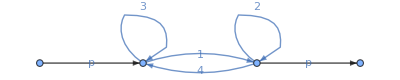
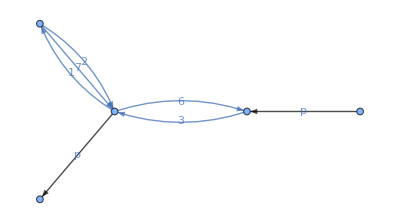
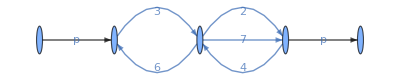
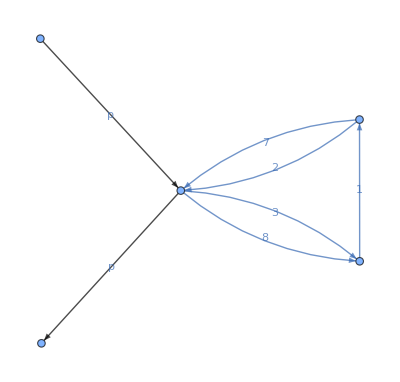
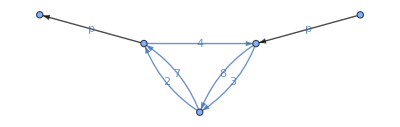
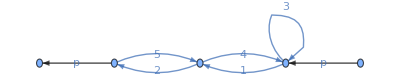
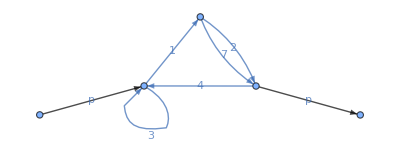
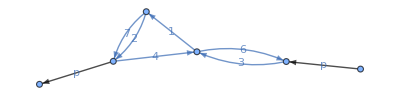
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[j[MastersPANPA[[k,1]]//ToExpression,MastersPANPA[[k,6]]]//drawDiagram,{k,LMastersPANPA}]//DeleteDuplicates
```

GMs:

```mathematica
Table[der[MastersPANPA[[i]],s],{i,LMastersPANPA}]/.InputReduzePANPA;
GMs=Table[Coefficient[%[[i]],MastersPANPA[[j]]],{i,LMastersPANPA},{j,LMastersPANPA}]//Factor;
%//MatrixForm
```

GMm12:

```mathematica
Table[der[MastersPANPA[[i]],m2],{i,LMastersPANPA}]/.InputReduzePANPA;
GMm2=Table[Coefficient[%[[i]],MastersPANPA[[j]]],{i,LMastersPANPA},{j,LMastersPANPA}]//Factor;
%//MatrixForm
```

Checks:

```mathematica
D[GMs,m2]-D[GMm2,s]-(GMm2.GMs-GMs.GMm2)//Simplify//Flatten//Union
s GMs+m2 GMm2-DiagonalMatrix[1/2 Table[InputReduzePANPA[[k,2]]/._INT->1//Factor,{k,3,Length[InputReduzePANPA],3}]]//Simplify//Simplify//Flatten//Union
```

{0}

{0}

Everything is fine!

We take for simplicity from now on m2=1.

```mathematica
GMsPANPA=GMs/.{m2->1}//Factor;
%//MatrixForm
```

```mathematica
MITally=MastersPANPA/.{INT[X_,Y_,Z_,U__]->INT[X,Y,Z]}//Tally//SortBy[#,#[[2]]&]&//Reverse;
Table[{"Number of master integrals in a sector",k,"Number of sectors of that type",Length[Cases[MITally,{_INT,k}]]},{k,5}]//TableForm
```

Number of master integrals in a sector | 1 | Number of sectors of that type | 22
Number of master integrals in a sector | 2 | Number of sectors of that type | 4
Number of master integrals in a sector | 3 | Number of sectors of that type | 6
Number of master integrals in a sector | 4 | Number of sectors of that type | 1
Number of master integrals in a sector | 5 | Number of sectors of that type | 0

1x K3 sector (3x3), 1x Elliptic sector with third kind (3x3), 3x Elliptic sector (2x2)

## Sectors with 4 Master Integrals -> 1

```mathematica
Cases[MITally,{_INT,4}]
```

{{INT[PA,7,477],4}}

```mathematica
Position[MastersPANPA,477][[All,1]]
GMsPANPA[[%,%]];
Rotation[s][{%,({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})}];
Ableitungsbasis[s,4][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector2035.txt",%];
```

{45,46,47,48}

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | -(12 (-23+4 s+s^2))/((-4+s)^2 s^2 (5+s)) | -(3 (-120+448 s-231 s^2+3 s^3+8 s^4))/((-4+s)^2 (-1+s) s^2 (5+s)) | -(110-177 s+21 s^2+10 s^3)/((-4+s) (-1+s) s (5+s)))

{0, (-12*(-23 + 4*s + s^2))/((-4 + s)^2*s^2*(5 + s)), (-3*(-120 + 448*s - 231*s^2 + 3*s^3 + 8*s^4))/((-4 + s)^2*(-1 + s)*s^2*(5 + s)), 
 -((110 - 177*s + 21*s^2 + 10*s^3)/((-4 + s)*(-1 + s)*s*(5 + s)))}

This sector turns out to be	DLOGS

## Sectors with 3 Master Integrals -> 6

```mathematica
Cases[MITally,{_INT,3}]
```

{{INT[PA,7,247],3},{INT[PA,6,462],3},{INT[PA,6,222],3},{INT[PA,5,213],3},{INT[PA,5,206],3},{INT[PA,4,212],3}}

```mathematica
Position[MastersPANPA,247][[All,1]]
GMsPANPA[[%,%]];
(*Rotation[s][{%,({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}})}];*)
Ableitungsbasis[s,3][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector247.txt",%];
```

{40,41,42}

(0 | 1 | 0
0 | 0 | 1
-(-3+2 s)/((-4+s) (-1+s) s^2) | -((-1+2 s) (-12+5 s))/((-4+s) (-1+s) s^2) | -(18-28 s+7 s^2)/((-4+s) (-1+s) s))

{-((-3 + 2*s)/((-4 + s)*(-1 + s)*s^2)), -(((-1 + 2*s)*(-12 + 5*s))/((-4 + s)*(-1 + s)*s^2)), -((18 - 28*s + 7*s^2)/((-4 + s)*(-1 + s)*s))}

This sector turns out to be	DLOGS

```mathematica
Position[MastersPANPA,462][[All,1]]
GMsPANPA[[%,%]];
(*Rotation[s][{%,({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}})}];*)
Ableitungsbasis[s,3][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector462.txt",%];
```

{33,34,35}

(0 | 1 | 0
0 | 0 | 1
0 | -(2 (-8+24 s-8 s^2+s^3))/((-2+s) s^2 (4-8 s+s^2)) | -(2 (-16+42 s-19 s^2+2 s^3))/((-2+s) s (4-8 s+s^2)))

{0, (-2*(-8 + 24*s - 8*s^2 + s^3))/((-2 + s)*s^2*(4 - 8*s + s^2)), (-2*(-16 + 42*s - 19*s^2 + 2*s^3))/((-2 + s)*s*(4 - 8*s + s^2))}

This sector turns out to be	DLOGS

```mathematica
Position[MastersPANPA,222][[All,1]]
GMsPANPA[[%,%]];
(*Rotation[s][{%,({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}})}];*)
Ableitungsbasis[s,3][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector222.txt",%];
```

{27,28,29}

(0 | 1 | 0
0 | 0 | 1
0 | -(2 (18-11 s+2 s^2))/((-4+s) (-3+s) s^2) | -(54-32 s+5 s^2)/((-4+s) (-3+s) s))

{0, (-2*(18 - 11*s + 2*s^2))/((-4 + s)*(-3 + s)*s^2), -((54 - 32*s + 5*s^2)/((-4 + s)*(-3 + s)*s))}

This sector turns out to be	DLOGS

```mathematica
Position[MastersPANPA,213][[All,1]]
GMsPANPA[[%,%]];
Rotation[s][{%,({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}})}];
Ableitungsbasis[s,3][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector213.txt",%];
```

{17,18,19}

(0 | 1 | 0
0 | 0 | 1
-(2 (6-3 s+s^2))/((-9+s) (-1+s)^2 s^2) | (2 (12-5 s+s^2))/((-9+s) (-1+s)^2 s) | -(-3+s)/((-1+s) s))

{(-2*(6 - 3*s + s^2))/((-9 + s)*(-1 + s)^2*s^2), (2*(12 - 5*s + s^2))/((-9 + s)*(-1 + s)^2*s), -((-3 + s)/((-1 + s)*s))}

This sector turns out to be	ELLIPTIC WITH THIRD KIND

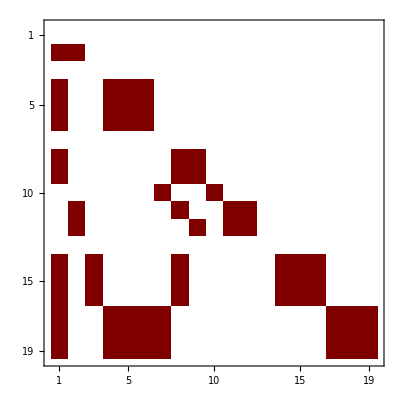

```mathematica
GMsPANPA[[;;19,;;19]]//MatrixPlot
```

Coupling to K3!!!

```mathematica
Position[MastersPANPA,206][[All,1]]
GMsPANPA[[%,%]];
(*Rotation[s][{%,({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}})}];*)
Ableitungsbasis[s,3][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector206.txt",%];
```

{14,15,16}

(0 | 1 | 0
0 | 0 | 1
0 | (2 (-9+5 s))/((-9+s) (-1+s) s^2) | -(36-35 s+3 s^2)/((-9+s) (-1+s) s))

{0, (2*(-9 + 5*s))/((-9 + s)*(-1 + s)*s^2), -((36 - 35*s + 3*s^2)/((-9 + s)*(-1 + s)*s))}

This sector turns out to be	DLOGS

```mathematica
Position[MastersPANPA,212][[All,1]]
GMsPANPA[[%,%]];
(*Rotation[s][{%,({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}})}];*)
Ableitungsbasis[s,3][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector212.txt",%];
```

{4,5,6}

(0 | 1 | 0
0 | 0 | 1
12/((-16+s) (-4+s) s^2) | -24/((-16+s) (-4+s) s) | (6 (-32+5 s))/((-16+s) (-4+s) s))

{12/((-16 + s)*(-4 + s)*s^2), -24/((-16 + s)*(-4 + s)*s), (6*(-32 + 5*s))/((-16 + s)*(-4 + s)*s)}

This sector turns out to be	K3

## Sectors with 2 Master Integrals -> 4

```mathematica
Cases[MITally,{_INT,2}]
```

{{INT[PA,6,246],2},{INT[PA,5,110],2},{INT[PA,4,78],2},{INT[NPA,8,479],2}}

```mathematica
Position[MastersPANPA,246][[All,1]]
GMsPANPA[[%,%]];
Ableitungsbasis[s,2][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector246.txt",%];
```

{30,31}

(0 | 1
-2/((-4+s) s^2) | -(2 (-3+s))/((-4+s) s))

{-2/((-4 + s)*s^2), (-2*(-3 + s))/((-4 + s)*s)}

This sector turns out to be	DLOGS

```mathematica
Position[MastersPANPA,110][[All,1]]
GMsPANPA[[%,%]];
Ableitungsbasis[s,2][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector110.txt",%];
```

{11,12}

(0 | 1
-(4 (27+6 s-14 s^2+2 s^3))/((-9+s) (-4+s)^2 (-1+s) s^2) | (2 (54-49 s+7 s^2))/((-9+s) (-4+s) (-1+s) s))

{(-4*(27 + 6*s - 14*s^2 + 2*s^3))/((-9 + s)*(-4 + s)^2*(-1 + s)*s^2), (2*(54 - 49*s + 7*s^2))/((-9 + s)*(-4 + s)*(-1 + s)*s)}

This sector turns out to be	ELLIPTIC

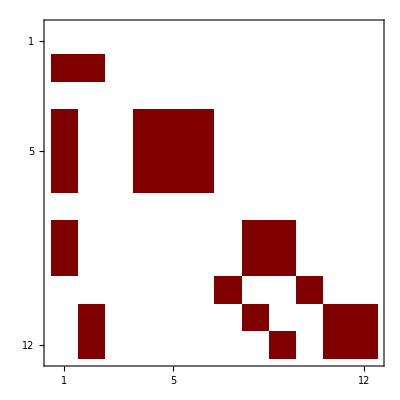

```mathematica
GMsPANPA[[;;12,;;12]]//MatrixPlot
```

Coupling to Elliptic 2x2!!!

```mathematica
Position[MastersPANPA,78][[All,1]]
GMsPANPA[[%,%]];
Ableitungsbasis[s,2][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector78.txt",%];
```

{8,9}

(0 | 1
-4/((-9+s) (-1+s) s) | (2 (-9+5 s))/((-9+s) (-1+s) s))

{-4/((-9 + s)*(-1 + s)*s), (2*(-9 + 5*s))/((-9 + s)*(-1 + s)*s)}

This sector turns out to be	ELLIPTIC

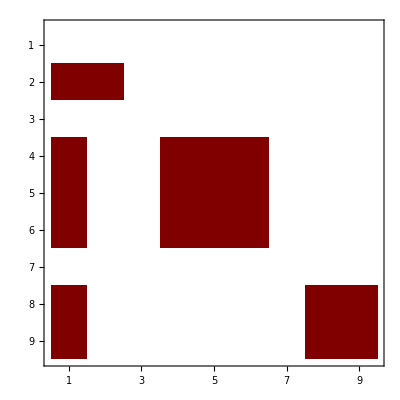

```mathematica
GMsPANPA[[;;9,;;9]]//MatrixPlot
```

No interesting couplings.

```mathematica
GMsPANPA[[51;;52,51;;52]];
Ableitungsbasis[s,2][%]/.ϵ->0//Factor//MatrixForm
%[[-1]]//InputForm
Export["/Users/Chris2106Nega/Desktop/Projekt_Mattia_AEI/DGLS_Sectors/Sector479.txt",%];
```

(0 | 1
-(2 (32-84 s-4 s^2+9 s^3+2 s^4))/((-4+s) (-1+s) s^2 (2+s) (8+s)) | -(192-224 s-78 s^2+24 s^3+5 s^4)/((-4+s) (-1+s) s (2+s) (8+s)))

{(-2*(32 - 84*s - 4*s^2 + 9*s^3 + 2*s^4))/((-4 + s)*(-1 + s)*s^2*(2 + s)*(8 + s)), -((192 - 224*s - 78*s^2 + 24*s^3 + 5*s^4)/((-4 + s)*(-1 + s)*s*(2 + s)*(8 + s)))}

This sector turns out to be	ELLIPTIC

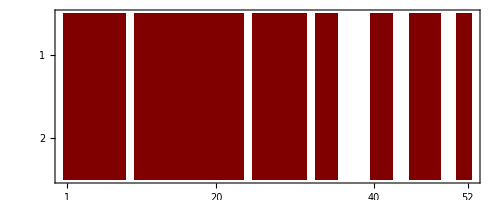

```mathematica
GMsPANPA[[51;;52,;;52]]//MatrixPlot
```

Coupling to everything!!!